```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/xxx-xxx/Desktop/Summer-2017-Machine_Learning/HW2

```mathematica
dataset = Import["HTRU_2.csv"];
```

```mathematica
key = dataset[[All,1;;-2]];
```

```mathematica
value = dataset[[All,-1]];
```

```mathematica
dataset = Thread[key->value];
```

```mathematica
n=Length[dataset];
rs=RandomSample[Range[n]];
cut=Ceiling[.9 n];
train=dataset[[rs[[1;;cut]]]];
test=dataset[[rs[[cut+1;;]]]];
```

```mathematica
classifier=Classify[train,Method->"SupportVectorMachine"]
```

ClassifierFunction[…]

```mathematica
cm = ClassifierMeasurements[classifier,test]
```

ClassifierMeasurementsObject[…]

```mathematica
cm["Accuracy"]
```

0.982672

```mathematica
features=DimensionReduce[train[[All,1]],2]
```

{{-0.62298,-0.802404},{-2.71454,4.68529},{0.456525,-1.57673},{0.0969353,-0.991221},16102,{-1.48926,1.45778},{-6.02588,5.59734},{-3.15939,1.95871}}
 |  |  |  |

```mathematica
group=GroupBy[Thread[features->train[[All,2]]],Last->First]
```

<|0→{{-0.62298,-0.802404},{-2.71454,4.68529},{0.456525,-1.57673},14628,{-1.48926,1.45778},{-6.02588,5.59734},{-3.15939,1.95871}},1→{1}|>
 |  |  |  |

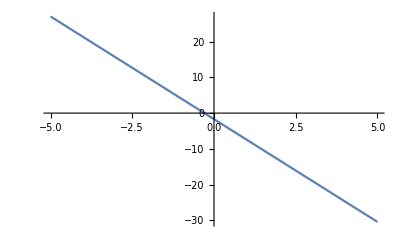

```mathematica
Plot[-5.742753657931802x-1.6988399411045867,{x,-5,5}]
```

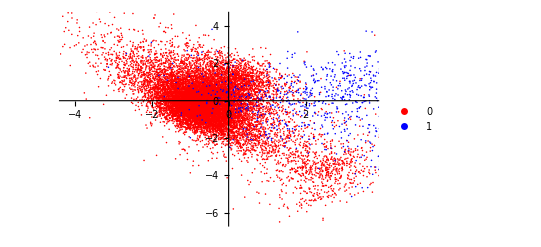

```mathematica
ListPlot[Values[group],PlotLegends->Keys[group],PlotStyle->{Red,Blue}]
```

```mathematica
Options[classifier]
```

{<|Basic→<|ExampleNumber→16109,FeatureNumber→8,ClassNumber→2|>,Input→<|Preprocessor→ToMLDataset,Processor→  ToVector→ImputeMissing→Standardize|>,Output→<|Preprocessor→ToMLDataset,Processor→  ToVector→IntegerEncodeNominalVector→FromVector→FirstValues,ProbabilityPostprocessor→Identity,Name→class,Marginal→<|0→0.908386,1→0.0916144|>|>,Combiner→First,Decision→<|Prior→Automatic,Utility→SparseArray[<2>, {2, 3}],Threshold→0,TieBreaker→RandomChoice,PerformanceGoal→Automatic,BatchProcessing→Automatic|>,Models→{<|Method→SupportVectorMachine,SVMParameters→<|DataSize→All,CrossValidation→Automatic,KernelType→RadialBasisFunction,GammaScalingParameter→1/(8 √2),SoftMarginParameter→45.2548,PolynomialDegree→3,BiasParameter→0,MulticlassMethod→Automatic,HyperparameterOptimizationMethod→Automatic,shrinking→True,cacheSize→100|>,HyperparameterOptimizationMethod→GridSearch,TrainedModel→{<|supportVectors→{{0.868085,0.456073,-0.171134,-0.291005,-0.402354,-0.834249,2.28883,2.80029},{-1.15009,-0.573964,0.547984,0.0681606,-0.324642,-0.27781,-0.152158,-0.399286},{0.890394,0.574268,-0.445971,-0.364514,-0.331603,-0.211836,0.0899974,-0.248237},{-0.475937,-0.444185,0.114717,-0.0664887,-0.0961295,0.736301,-0.838043,-0.795579},{-0.797426,0.165659,0.0740665,-0.202897,0.365175,1.71674,-1.30576,-0.94274},{-0.564255,2.03586,0.00307333,-0.412304,0.358186,1.2915,-1.24481,-0.918695},{-1.84685,-1.32568,0.70822,0.324492,1.95992,2.21296,-1.70921,-0.989408},{0.780072,0.760165,-0.532917,-0.35423,-0.335654,-0.211657,0.0093661,-0.327975},{-0.516582,0.185246,0.231351,-0.131301,0.852356,2.12878,-1.49941,-0.975993},{-0.969478,-0.1287,0.549029,0.0415379,-0.333001,-0.281504,0.101875,-0.205851},{0.184156,0.289276,-0.390965,-0.328814,-0.372313,-0.529784,0.695484,0.339045},{-1.26408,-1.42452,0.535214,0.271497,-0.144343,0.509305,-0.82921,-0.793349},{-1.16323,-1.58236,0.608053,0.327493,-0.0614104,1.12196,-0.895141,-0.830276},{0.20188,-1.01843,0.221178,-0.0150132,-0.302305,-0.205487,-0.110947,-0.34494},{0.26575,0.561341,0.109191,-0.225564,-0.387262,-0.718176,1.12673,0.998453},{-0.922416,-0.371444,0.928208,0.263534,0.714363,1.90819,-1.49436,-0.975209},{-0.123888,-0.226675,0.0822413,-0.159309,-0.359704,-0.347289,0.41149,0.00440945},{0.891005,0.885032,-0.580352,-0.386765,-0.331717,-0.285105,-0.0503216,-0.334115},{0.0298284,1.08641,-0.0128198,-0.298689,-0.0994388,0.661116,-0.892768,-0.817834},{0.940512,1.80804,-0.380274,-0.39173,-0.263563,0.170281,-0.279824,-0.509213},{-1.14642,-0.732529,0.489446,0.108741,-0.319764,-0.358116,-0.0674793,-0.299177},{-0.0872158,0.01366,0.324065,-0.107232,-0.320877,-0.219962,0.154278,-0.185479},{-0.0425984,1.28259,0.0555551,-0.276181,3.55015,3.34511,-1.89972,-0.998986},{0.362319,-1.26455,-0.448506,-0.148119,-0.357364,-0.54493,0.372331,0.132239},{-0.162699,-1.48373,-0.224231,-0.0802475,-0.373683,-0.749549,0.977952,1.03388},{-0.0969949,0.143417,0.313938,-0.160258,-0.309608,-0.180978,0.115417,-0.196139},{-0.337806,-0.0742651,-0.158519,-0.294766,-0.391256,-0.647462,1.23984,0.93659},{-0.432236,0.315458,0.167995,-0.227946,0.0468265,1.1351,-1.07531,-0.883501},{-1.28363,-0.501935,0.442331,0.0891342,-0.401869,-0.805636,2.05843,2.33072},{-0.932195,-0.189474,0.328085,-0.0393021,0.0907033,1.21422,-1.12525,-0.897312},{0.742178,1.28671,-0.322275,-0.396631,-0.340875,-0.286401,0.266339,-0.0856379},{-0.835015,-0.168071,0.330864,-0.089431,-0.316027,-0.161003,-0.14193,-0.410767},{-0.603983,0.711526,0.135879,-0.260345,0.572349,2.04106,-1.40839,-0.963352},{-0.407177,-1.01756,0.238782,0.0252749,-0.324129,-0.224893,-0.126242,-0.398651},{1.15901,1.05964,-0.45085,-0.396234,-0.334513,-0.367597,0.0446673,-0.237202},{-0.230847,0.113019,0.186532,-0.220787,-0.279425,-0.0154734,-0.137329,-0.399965},{-1.60176,1.47805,0.361869,-0.327448,5.48206,2.94056,-2.07514,-0.991155},{-0.971312,1.44131,0.699757,-0.128941,1.70011,3.02295,-1.64545,-0.991622},{0.131287,1.89499,-0.137378,-0.367965,0.211379,1.44869,-1.23057,-0.926005},{-0.830737,-0.0690152,0.28786,-0.140822,-0.287727,-0.0964903,-0.318902,-0.519511},{0.869918,-1.07543,-0.598376,-0.194085,-0.312575,-0.410643,-0.243964,-0.397323},{0.657833,0.477389,-0.123506,-0.321456,0.0847693,1.20488,-1.12818,-0.899013},{0.0915593,-1.18221,-0.312259,-0.143265,-0.371771,-0.48499,0.643091,0.247909},{-0.494884,0.789301,-0.0379618,-0.265161,-0.129251,0.875356,-0.787675,-0.789482},{-0.430403,-0.00944474,0.10987,-0.182199,-0.0875139,0.553553,-0.948856,-0.829207},{-2.16009,-1.92257,1.59871,1.26952,2.11365,2.60454,-1.7876,-0.998803},{-3.04021,-1.03243,3.83902,3.10056,1.57547,1.8872,-1.68408,-0.993251},{-0.599093,0.0438657,0.615042,-0.0634143,3.61839,3.8253,-1.86759,-1.00037},{0.253221,-0.353748,-0.395177,-0.281006,-0.348977,-0.284791,0.260928,-0.115574},{-0.0031762,0.572293,0.177679,-0.198665,-0.129194,0.60268,-0.831452,-0.79297},{-0.445683,-0.500394,0.0447784,-0.0787709,-0.287327,0.0529047,-0.248738,-0.491955},{-0.00928817,-1.21269,0.105992,0.0216124,0.00232215,0.923372,-1.06496,-0.879025},{-0.616207,-0.175987,0.253216,-0.0722892,0.427824,0.856111,-1.5086,-0.972338},{0.572877,0.323506,-0.219703,-0.320006,-0.399187,-0.710933,1.84043,1.71012},{0.580211,1.96304,-0.402899,-0.385553,-0.327581,-0.494069,-0.0799655,-0.231791},{1.38944,0.566683,-0.55646,-0.347379,-0.266787,0.111735,-0.359963,-0.554714},{1.08139,0.668527,-0.738199,-0.33223,-0.257287,0.147492,-0.449513,-0.607372},{-0.218929,4.31996,0.108959,-0.454066,0.386971,0.922556,-1.45479,-0.960027},{-0.918749,-0.0703481,0.319051,-0.0974437,-0.390857,-0.797043,1.60144,1.81841},{0.152068,0.361551,-0.403567,-0.324658,-0.382412,-0.589224,0.869093,0.50087},{-0.430403,0.555502,0.135465,-0.228146,1.55319,2.82269,-1.65098,-0.99258},{0.488532,1.31084,-0.383641,-0.413849,-0.359647,-0.50798,0.212449,-0.0875635},{0.0542763,0.903042,-0.240546,-0.372868,-0.372513,-0.690257,0.732183,0.614474},{-2.11456,5.73998,0.881993,-0.271989,5.99729,1.97609,-2.20025,-0.970771},{0.0545819,-0.307298,0.0618851,-0.129616,-0.221655,0.373068,-0.557941,-0.6712},{-0.895218,0.402408,0.854947,0.0548979,3.10565,3.63963,-1.81949,-1.00038},{-0.493356,1.48983,0.025538,-0.317712,0.203305,1.33732,-1.25624,-0.932082},{0.464389,0.0316472,-0.374715,-0.340049,-0.353199,-0.611484,0.33464,0.16118},{-1.28669,-0.0646625,0.87909,0.0697707,2.60266,3.04573,-1.82194,-1.0007},{0.750429,1.00764,-0.630692,-0.379206,-0.334684,-0.325733,-0.0544075,-0.331562},{-0.812095,-1.15011,0.432548,0.215861,-0.346695,-0.452048,0.196293,-0.0824175},{-1.19654,-0.442923,0.686439,0.0734726,1.95675,3.1861,-1.6629,-0.992336},{-0.251322,-0.149365,0.12701,-0.135095,-0.296684,-0.132883,-0.0436895,-0.327294},{-0.0762142,-0.897055,0.22619,0.0445829,-0.313859,-0.127494,-0.190423,-0.454774},{0.20188,0.283807,-0.0571414,-0.186936,-0.3718,-0.515537,0.575445,0.201361},{-1.01593,-0.660553,0.243949,0.02404,-0.328494,-0.219697,0.0591703,-0.25702},{-0.482049,-0.764613,0.374643,-0.0259274,-0.299052,-0.329042,-0.110739,-0.284566},{-2.95954,-1.75274,4.08187,3.7842,0.68244,2.00906,-1.46141,-0.970834},{-1.09477,-0.64133,0.400628,0.0325965,-0.294973,-0.207009,-0.340036,-0.513161},{-1.00371,0.781202,0.219888,-0.218649,0.470759,1.55312,-1.39205,-0.957643},{-0.762588,0.151568,0.350132,-0.0698962,-0.391313,-0.775223,1.50958,1.59623},{-1.14978,-1.85609,0.529442,0.469922,-0.35571,-0.401984,0.332638,-0.0149286},{0.0906425,0.464419,-0.394138,-0.376899,-0.376165,-0.651826,1.0427,0.816677},{-1.0801,-1.7366,0.572342,0.312411,-0.374966,-0.566667,0.815187,0.515326},{0.961904,0.222449,-0.446648,-0.344588,-0.34407,-0.332912,0.0782688,-0.248819},{-0.794676,0.765446,0.5321,-0.126441,-0.310949,-0.155615,0.033919,-0.284002},{-0.983841,-0.0962641,0.436283,-0.0431548,-0.355225,-0.418153,0.383363,0.0363431},{-0.40351,0.249041,0.133757,-0.166871,2.05412,3.38294,-1.7138,-0.997809},{-0.533695,-0.378144,0.328589,0.0463605,-0.364183,-0.421703,0.523297,0.136666},{0.656,1.27941,-0.251422,-0.356808,-0.128424,0.833853,-0.81185,-0.799038},{-0.322527,-0.43429,0.19477,-0.0920509,-0.279282,-0.0155615,-0.394167,-0.565879},{-1.90583,-0.655764,1.69516,0.788307,4.38395,2.0502,-1.84505,-0.994205},{0.616577,0.363116,-0.314575,-0.360324,-0.360217,-0.41401,0.306021,-0.0739909},{0.0411356,-1.75115,-0.176174,0.0269055,1.77682,0.876551,-1.59221,-0.97829},{-0.416345,0.973494,0.310285,-0.18302,-0.304501,-0.144996,-0.0713242,-0.352113},{-0.522693,0.732892,0.297754,-0.209211,-0.336852,-0.299054,0.363779,0.0062039},{0.206464,0.262815,0.104412,-0.234075,-0.115443,0.492583,-0.837934,-0.782139},{-0.133361,-0.206766,0.0808941,-0.14082,-0.407917,-0.792994,2.62396,2.9424},{0.111729,3.40412,-0.437008,-0.504874,4.5833,3.31681,-1.96333,-0.996018},{-1.50733,-1.00743,0.867732,0.43683,-0.153985,0.574752,-0.731076,-0.749407},{-0.657157,-0.37365,0.131554,-0.105587,0.075897,1.41587,-1.09274,-0.894536},{-0.181646,-1.68021,-0.246274,0.0533262,-0.390514,-0.754194,1.53079,1.55497},{-0.259573,-1.49304,-0.355696,0.019109,-0.401698,-0.855868,2.34692,3.09082},{0.551485,-0.360185,-0.743625,-0.25101,-0.32216,-0.458046,-0.164582,-0.326956},{-0.64096,-0.404876,0.261725,-0.0552489,-0.264191,-0.0610357,-0.491089,-0.60022},{-2.07819,-1.62634,1.97039,1.31312,0.623957,1.97954,-1.43125,-0.966091},{-0.226263,-1.02914,-0.310323,-0.155583,-0.381414,-0.683318,0.880146,0.700102},{0.950902,0.0494147,-0.632576,-0.285675,-0.318309,-0.206319,-0.210352,-0.458841},{-1.83493,-2.50072,1.97724,1.95952,-0.283133,0.0726901,-0.32313,-0.542537},{0.805132,1.40554,-0.429383,-0.400529,-0.348321,-0.552125,0.122847,-0.0846428},{-0.511692,-0.00316076,0.259626,-0.0900665,-0.285387,-0.161586,-0.269662,-0.449263},{1.16757,0.523465,-0.555156,-0.2913,-0.25509,0.226309,-0.438789,-0.608222},{1.25619,0.492666,-0.397737,-0.375281,-0.341931,-0.322246,0.0570605,-0.267514},{-0.128166,0.409912,0.0938352,-0.228939,-0.401298,-0.758589,1.82296,1.79237},{-1.04557,-0.200792,0.301919,-0.120195,-0.308039,-0.219647,0.0287878,-0.255545},{-1.26132,-0.661833,0.322925,-0.0586714,0.126364,1.41439,-1.13674,-0.903099},{0.753485,0.716484,-0.355461,-0.405192,-0.33069,-0.272364,-0.0161916,-0.306625},{-0.222901,0.837004,-0.0128128,-0.279231,0.324408,1.45255,-1.27184,-0.930987},{-1.10119,0.621117,0.741892,0.014217,4.20644,3.67769,-1.96811,-0.99851},{0.259944,0.457723,-0.0407134,-0.236853,-0.37063,-0.763357,0.85003,1.04119},{-0.93739,0.542165,1.48391,0.405614,1.46135,1.2007,-1.58666,-0.966164},{-1.20876,2.75271,0.323592,-0.374808,-0.262679,0.424573,-0.290604,-0.543294},{-0.41604,-0.801679,0.594983,0.0839937,-0.355339,-0.543265,0.675896,0.39605},{-0.406566,0.0543117,0.14837,-0.162635,-0.105943,0.574566,-0.901625,-0.818698},{0.375766,0.574202,-0.121899,-0.256395,-0.401469,-0.745405,2.07687,2.10565},{-0.107996,-0.137276,0.15284,-0.129872,-0.324985,-0.282559,0.0541941,-0.236426},{-0.247044,0.182307,-0.138456,-0.272984,-0.401669,-0.833357,2.26141,2.77839},{-0.478687,-0.295211,0.264809,-0.0627979,-0.173812,0.360317,-0.762538,-0.757802},{0.318925,0.0111973,-0.445126,-0.303278,-0.368491,-0.54316,0.514939,0.188815},{-0.828597,-0.576248,0.587905,0.0679956,0.93252,2.08001,-1.54652,-0.981188},{-1.25521,-2.08778,0.642609,0.624425,-0.356052,-0.389773,0.28169,-0.08753},{0.219299,-0.847685,-0.435673,-0.245054,-0.367036,-0.71519,0.77342,0.761367},{1.24061,0.113667,-0.755011,-0.299028,-0.227931,0.132806,-0.546642,-0.652196},{0.419161,-0.591255,0.00518146,-0.133825,-0.0575876,0.758066,-0.950795,-0.838204},{0.828051,0.868426,-0.586488,-0.361508,-0.305814,-0.0942514,-0.126735,-0.408621},{-0.71522,1.35885,0.728286,-0.121362,4.98336,2.99498,-2.00691,-0.991959},{-0.383341,-0.779048,-0.319544,-0.194469,-0.393054,-0.766726,1.46933,1.50557},{-3.26697,-0.906017,3.52543,2.63156,-0.309123,-0.270219,-0.0785925,-0.326464},{-1.33467,-1.04113,0.417803,0.122506,-0.124886,0.606552,-0.871497,-0.811454},{-1.87099,-1.94334,1.5307,1.39875,-0.343443,-0.231084,0.222268,-0.156674},{-3.04755,2.25637,1.94328,0.543504,3.7551,4.05498,-1.87291,-1.00138},{0.304867,-0.69501,0.127779,-0.0383731,-0.21612,0.130931,-0.719125,-0.734976},{-1.05291,0.989763,0.753347,-0.0406439,-0.103404,0.372935,-0.76512,-0.731006},{-1.24604,-0.401432,0.588077,0.113709,-0.372,-0.638591,0.824786,0.635906},{-1.28608,0.057453,0.731013,-0.0352444,-0.286528,-0.347749,-0.417372,-0.505987},{0.0976713,-0.81524,-0.0615841,-0.147042,-0.401099,-0.768868,1.8789,1.8962},{-2.16895,-2.12906,1.70141,1.58405,0.0945546,0.984457,-1.17962,-0.908365},{0.59488,-0.370659,-0.408847,-0.256369,-0.345867,-0.408409,0.055142,-0.232532},{-1.44988,-0.367877,0.578248,0.0329407,-0.319108,-0.414669,0.00495474,-0.189417},{-0.2938,1.12342,0.332446,-0.253515,-0.383382,-0.664623,1.52226,1.34412},{-0.301746,1.06044,0.190497,-0.309158,0.284925,1.73996,-1.26519,-0.936575},{0.10745,0.0469942,-0.535263,-0.271223,-0.382726,-0.507611,1.01127,0.602249},{-0.780313,1.25568,0.382664,-0.258082,-0.263706,0.104856,-0.37199,-0.554758},{-0.108913,0.228012,0.00208691,-0.291989,0.202021,1.27512,-1.25712,-0.931032},{0.9781,1.66994,-0.300922,-0.377603,-0.346438,-0.522978,0.189205,-0.0428476},{0.532538,0.673844,-0.354962,-0.338139,-0.352543,-0.408642,0.294745,-0.05537},{-1.1565,-1.11539,0.368823,0.0823849,-0.283019,0.060421,-0.324963,-0.540591},{-0.92425,0.298826,0.580452,-0.0859659,0.0322485,0.816177,-1.16752,-0.907623},{-1.09844,-0.066244,1.13633,0.279768,1.58944,1.42282,-1.69289,-0.985834},{0.0185213,-0.298604,0.102322,-0.0409251,0.00817048,1.01946,-1.03488,-0.869614},{0.346428,0.768433,-0.348051,-0.346406,-0.373027,-0.540414,0.552303,0.191493},{1.24183,0.706223,-0.694345,-0.306031,-0.179261,0.520039,-0.714477,-0.749186},{0.901701,0.879171,-0.521964,-0.356749,-0.291549,-0.171528,-0.164752,-0.403143},{-0.303885,3.61451,0.0387587,-0.450392,0.179798,1.23023,-1.22949,-0.923736},{-0.686494,-0.44251,0.219607,-0.0166771,-0.00586552,1.32479,-0.9614,-0.85396},{-0.416651,-0.361559,0.0764334,-0.176335,1.11987,2.49369,-1.56529,-0.984776},{0.717119,3.2225,-0.215337,-0.470322,-0.196464,0.531307,-0.577467,-0.686208},{-0.57434,-0.56869,0.10738,-0.0825811,-0.119808,0.676546,-0.854821,-0.804942},{0.375766,0.696484,-0.221831,-0.35729,-0.37896,-0.639582,0.858092,0.6024},{-0.299912,-0.605865,0.335411,-0.0735253,-0.311605,-0.249753,-0.212906,-0.427468},{0.277974,-0.00419682,-0.10176,-0.295684,-0.402411,-0.750724,2.2291,2.361},{0.131287,-0.502693,-0.577014,-0.230014,-0.366151,-0.678714,0.506163,0.40973},{0.211048,1.07814,-0.294215,-0.386936,-0.367378,-0.666634,0.516555,0.387959},{-0.0746862,-1.04465,0.0570124,0.0223169,-0.345097,-0.335613,0.180065,-0.159444},{0.463778,0.718246,-0.435794,-0.384279,-0.346295,-0.563532,0.280147,0.0820574},{-0.300523,0.777455,0.245742,-0.201983,0.411192,1.89595,-1.33315,-0.950427},{0.382795,-0.997785,-0.413189,-0.22749,-0.395849,-0.693428,1.61698,1.44616},{-1.36034,-1.35962,0.734023,0.353452,-0.364439,-0.54154,0.610608,0.323101},{-0.106163,0.1125,-0.416177,-0.340049,-0.369118,-0.639446,0.591776,0.363758},{-0.728667,-0.101244,0.149359,-0.192705,0.193263,1.736,-1.17685,-0.917414},{0.488532,0.78187,-0.176728,-0.31924,0.563106,2.12631,-1.42005,-0.968058},{-0.155364,1.34548,0.0417317,-0.280049,3.6118,3.56537,-1.90609,-0.999962},{0.00813094,-0.759976,-0.396459,-0.211381,-0.363584,-0.563297,0.468649,0.18932},{-0.473492,-0.732385,0.119072,-0.0301739,-0.40418,-0.891107,2.91617,4.24959},{1.14404,1.22555,-0.320194,-0.365355,-0.346381,-0.430692,0.200906,-0.0758315},{-0.557226,-0.483032,0.199556,-0.0808417,-0.0866295,0.780332,-0.890341,-0.817153},{-0.650434,-1.24175,0.533628,0.186798,-0.259512,0.106528,-0.402982,-0.570391},{-1.44988,-1.25004,0.546669,0.313666,-0.361187,-0.499681,0.601586,0.276798},{-0.375701,1.81258,-0.00305198,-0.347823,-0.154099,0.505601,-0.773356,-0.765791},{-1.07797,0.470046,0.748403,-0.0103049,2.96897,2.57483,-1.76821,-0.993062},{-2.11883,-1.27615,1.84422,1.23133,-0.0804959,0.751276,-0.919939,-0.827719},{-0.378145,-0.731866,-0.390491,-0.194656,-0.382355,-0.736454,1.07088,1.06074},{-1.60146,0.923935,1.09829,0.0177785,4.34367,1.75307,-2.04284,-0.976883},{0.0943097,0.244159,0.195434,-0.203706,0.0848264,0.980459,-1.1514,-0.901243},{-0.440488,-1.08176,0.25529,0.0109871,-0.134443,0.460509,-0.811814,-0.772153},{0.397769,0.567848,-0.454135,-0.350256,-0.36501,-0.519389,0.411477,0.0844843},{-1.38754,1.71197,0.687025,-0.135932,1.2695,2.11145,-1.58839,-0.980871},{0.548429,-1.37706,-0.327828,-0.149683,-0.361758,-0.549663,0.391145,0.113433},{-0.78887,0.0853894,0.408115,-0.160997,-0.166852,0.430893,-0.773736,-0.767377},{-1.30136,-0.133911,0.724803,0.0827456,1.70036,1.98047,-1.59754,-0.978199},{-2.03816,-1.41296,1.11021,0.692333,-0.165482,0.440738,-0.788968,-0.77283},{-0.663269,-0.664912,0.43675,-0.0292533,-0.32256,-0.261348,-0.0863003,-0.342533},{0.248942,0.182926,0.0143053,-0.243783,0.246269,1.19258,-1.31241,-0.941894},{1.08689,1.5471,-0.357473,-0.385948,-0.333229,-0.506116,-0.0101542,-0.206857},{0.639497,1.04348,-0.440437,-0.376493,-0.312204,-0.183243,0.0186265,-0.291283},{-0.921194,-0.05153,0.200119,-0.0792773,-0.222625,0.182784,-0.694538,-0.733721},{0.57196,0.273298,-0.560901,-0.337648,-0.344042,-0.511524,0.0596293,-0.160976},{-0.769617,-1.67744,0.360209,0.253585,-0.381442,-0.532433,0.997109,0.619044},{-0.0762142,-0.158844,0.333552,-0.0900308,-0.255889,-0.0416514,-0.603599,-0.674158},{0.45461,0.510994,-0.370473,-0.352332,-0.343528,-0.4753,0.230294,-0.0272367},{-0.53614,0.44898,0.263488,-0.159803,-0.257772,0.337788,-0.406492,-0.60698},{-0.734168,-0.0914693,0.812033,0.108378,1.03713,2.26422,-1.53158,-0.978323},{0.9399,1.6373,-0.357814,-0.396105,-0.309579,-0.107361,-0.198365,-0.457435},{0.0701674,0.356738,0.0367455,-0.180063,-0.21786,0.318244,-0.601748,-0.691198},{0.134649,0.363235,-0.533385,-0.347487,-0.404436,-0.858844,2.79556,3.63014},{0.192712,-0.727028,-0.293766,-0.242228,-0.382954,-0.646421,0.910036,0.627709},{-0.253767,-1.04087,0.23236,0.00467645,0.31448,1.53457,-1.30533,-0.94145},{-1.60971,-0.932647,0.61772,0.157922,-0.30085,-0.223,-0.299878,-0.481854},{0.350707,0.411754,-0.11,-0.338869,-0.376079,-0.748112,1.11442,1.15412},{-0.0300689,-1.76792,-0.29493,0.0271981,-0.399444,-0.809197,1.86671,2.13854},{1.06183,-1.04813,-0.430197,-0.130501,-0.31791,-0.402386,-0.290237,-0.444914},{0.65875,-0.91531,-0.465922,-0.203294,-0.329264,-0.526331,-0.0167942,-0.169474},{-1.0688,0.0892305,0.514421,0.00399151,-0.290693,-0.015715,-0.329588,-0.540233},{0.754402,3.78095,-0.469505,-0.494042,-0.254149,0.0442151,-0.488787,-0.619105},{-0.668158,0.155394,0.210091,-0.195123,-0.155897,0.252955,-0.855238,-0.779053},{0.755319,0.869961,-0.391361,-0.376765,-0.336482,-0.357389,-0.00811643,-0.290534},{-0.66388,0.519524,0.843603,-0.0234795,1.34416,3.25881,-1.5806,-0.988764},{0.514813,0.48954,-0.6625,-0.342628,-0.328693,-0.448549,-0.00977485,-0.217106},{-0.361643,0.269586,0.405633,-0.0680351,-0.309922,-0.306217,0.0746575,-0.191198},{-0.997288,-0.139599,0.414267,-0.0797082,-0.284845,-0.124504,-0.223288,-0.436977},{-1.20051,-1.34262,0.554286,0.208775,-0.38943,-0.641172,1.24455,0.962731},{-1.47249,0.0244965,1.30237,0.462067,-0.17909,0.560922,-0.713061,-0.752786},{-1.0471,-0.293878,0.992977,0.244519,3.23585,3.64141,-1.86378,-1.00126},{0.485781,-1.36424,-0.392976,-0.0990137,-0.331461,-0.550351,0.00541351,-0.120438},{-0.874743,-0.980201,0.838406,0.299692,-0.364468,-0.725736,0.764149,0.772498},{-0.412372,-0.312657,-0.132237,-0.241423,-0.39719,-0.881929,2.58093,3.78833},{0.658139,0.906819,-0.236872,-0.336099,-0.360731,-0.517262,0.488888,0.175726},{1.68862,0.266166,-0.722148,-0.260968,-0.0545065,0.788574,-0.927523,-0.831017},{-0.927611,-0.724566,0.42642,0.115262,-0.392483,-0.75254,1.41344,1.37999},{0.69206,0.877272,-0.294227,-0.352218,-0.348663,-0.444171,0.129701,-0.171835},{-0.495801,-0.556755,0.326806,-0.00572759,-0.297512,-0.245194,-0.0374664,-0.279685},{0.251998,-0.876069,-0.0668695,-0.0482117,-0.317054,-0.277831,-0.00402532,-0.268131},{-0.434681,0.353786,0.0821567,-0.215315,-0.280138,0.0475607,-0.172862,-0.434319},{-0.0908829,0.892468,0.10808,-0.245923,-0.163571,0.360236,-0.762071,-0.753528},{-1.10425,0.0658569,0.942987,0.153228,4.27571,3.70224,-1.94267,-0.998706},{-2.10478,-1.77777,1.86453,1.36535,2.8522,2.74863,-1.7636,-0.993373},{-0.470131,0.464168,0.243333,-0.159991,-0.250468,0.0278944,-0.569811,-0.656418},{-0.346974,0.231116,0.438736,-0.0795474,1.42572,2.03021,-1.65285,-0.987189},{0.998575,-0.1575,-0.477182,-0.29157,-0.326611,-0.326749,-0.127874,-0.375054},{-0.509553,-1.10681,0.325235,0.0441345,-0.304558,-0.29531,-0.165025,-0.341315},{-1.95778,0.903285,1.35785,0.276724,0.140913,1.24101,-1.16185,-0.906276},{-0.594203,0.129544,0.344532,-0.0488026,-0.296627,-0.235714,-0.439053,-0.573126},{-0.172172,1.05981,-0.0117808,-0.343431,1.53664,2.93944,-1.62677,-0.990132},{-0.881772,-1.95013,0.522061,0.339658,-0.32022,-0.198455,-0.10504,-0.373724},{0.459194,-0.0228262,0.00829788,-0.269152,1.03519,2.77255,-1.54559,-0.985474},{-0.416345,-0.302082,0.134346,-0.106555,-0.057987,0.801661,-0.970786,-0.847559},{0.152985,0.542517,-0.343815,-0.352051,-0.384466,-0.711681,0.886256,0.755405},{-0.628125,0.529042,0.172436,-0.229657,-0.0834343,0.650991,-0.934253,-0.830723},{-0.734779,0.868821,0.345521,-0.242855,5.0625,3.22482,-2.0424,-0.990654},{-0.360421,0.173011,0.101858,-0.186405,-0.239342,0.229489,-0.488733,-0.630291},{0.390129,-0.452631,-0.507878,-0.302917,-0.343699,-0.400914,-0.0164942,-0.291575},{-1.40129,0.577679,1.62688,0.480069,1.64305,1.14901,-1.62914,-0.97019},{-1.0309,0.693829,0.735484,-0.0111878,-0.349006,-0.586898,0.638987,0.470462},{-0.859463,1.58044,0.823565,-0.0910744,0.284953,1.58399,-1.26882,-0.934334},{-0.728972,-0.0876789,0.558641,0.00110192,0.0696493,0.95746,-1.1169,-0.890224},{-1.13634,-1.7185,0.98113,0.682502,-0.260453,-0.0738784,-0.559093,-0.64025},{-1.00187,0.75456,0.712675,-0.0959888,3.49991,3.4948,-1.83192,-0.998681},{0.362319,0.560254,-0.615386,-0.326876,-0.350603,-0.493779,0.117044,-0.141742},{-2.03082,2.91228,0.97757,-0.0848827,3.14105,2.51563,-1.73056,-0.995338},{-0.17645,-2.10888,0.287749,0.211562,-0.348264,-0.160273,0.349736,-0.0834741},{-0.0911885,-0.528993,0.10518,-0.0744439,-0.150077,0.364848,-0.869944,-0.800977},{-2.0513,2.68427,0.991963,-0.0761656,2.94166,2.2656,-1.68067,-0.991554},{-0.423068,1.26997,0.0206801,-0.283862,1.09687,2.56288,-1.53704,-0.981192},{0.163375,0.514124,-0.084333,-0.294329,0.138431,1.28729,-1.15138,-0.904305},{-1.03579,-0.625298,0.590192,0.113485,-0.399016,-0.777373,2.017,2.20274},{-0.59237,-0.570064,0.183475,-0.0879121,-0.12055,0.505566,-0.90274,-0.817417},{-0.373867,-0.342306,0.0798104,-0.126741,-0.0483729,0.603916,-1.04213,-0.861338},{-0.509553,-0.221939,0.214313,-0.0777546,-0.340732,-0.312672,0.122097,-0.2061},{-0.637904,-0.115442,0.154385,-0.13599,-0.189018,0.376572,-0.746133,-0.758395},{-0.265685,-0.707514,0.00608914,-0.000529812,-0.219144,0.285525,-0.603234,-0.691116},{0.358958,1.19643,-0.164453,-0.361324,0.306064,1.88879,-1.23001,-0.927771},{0.399602,0.955119,-0.501127,-0.399596,-0.333343,-0.30796,0.0452112,-0.266891},{0.0380796,-1.7418,-0.422613,0.00380606,-0.358933,-0.622926,0.55306,0.386005},{0.265139,-0.236839,0.166087,-0.105155,-0.185623,0.123053,-0.794476,-0.754555},{-0.610706,0.0799121,0.281273,-0.0583611,-0.248043,-0.0949243,-0.521319,-0.605486},{-0.549892,0.977826,0.287341,-0.238073,5.12386,2.87703,-2.05465,-0.988422},{0.0933929,-0.443446,-0.369705,-0.234343,-0.401869,-0.72794,2.14134,2.1715},{-0.600621,-0.429874,0.402636,-0.0281857,-0.376878,-0.503168,0.804541,0.404867},{-0.499774,0.114166,0.0584829,-0.168633,-0.286757,0.203872,-0.241803,-0.51155},{0.872669,0.89254,-0.338432,-0.382822,-0.33768,-0.468092,0.273682,0.0202585},{-0.0328192,-1.33748,-0.416112,-0.0152795,-0.370516,-0.616097,0.631561,0.391469},{1.11042,1.05903,-0.394328,-0.37522,-0.342758,-0.274851,0.172258,-0.178317},{-2.29669,-0.928851,1.62394,0.776866,3.32309,4.14046,-1.83881,-1.00184},{0.585406,0.39957,-0.23286,-0.328184,-0.37956,-0.565138,1.02243,0.700778},{0.511757,1.52587,-0.24043,-0.377416,-0.340076,-0.265131,0.185312,-0.164704},{-1.2708,-1.66973,0.584623,0.361707,-0.293717,-0.082048,-0.335521,-0.53617},{-1.24116,-0.545793,0.634599,0.153097,-0.386121,-0.585624,1.22366,0.915808},{-0.268436,0.0305171,0.00740196,-0.274351,0.391536,1.82059,-1.29561,-0.939528},{-0.752198,0.0502566,0.39473,-0.12386,-0.393738,-0.801837,1.59253,1.83595},{0.582962,1.47491,-0.201038,-0.388829,-0.334627,-0.511224,0.107601,-0.0962167},{-0.357059,0.387724,0.162468,-0.295621,0.120744,0.968962,-1.16479,-0.902654},{0.411215,0.843062,-0.0435041,-0.279617,-0.240655,0.408747,-0.489457,-0.651989},{-0.744864,-1.61661,0.241655,0.134854,1.47453,3.20194,-1.62934,-0.993714},{-1.87436,-1.98847,1.46873,1.34756,0.166532,0.989245,-1.25522,-0.925604},{0.172543,0.605603,-0.00319163,-0.247923,-0.399786,-0.783662,1.76129,1.84725},{0.16857,0.290325,-0.330333,-0.344127,-0.372855,-0.635888,0.67056,0.440052},{0.314646,0.677357,-0.202985,-0.256086,-0.329521,-0.129781,0.0195556,-0.323736},{-0.905914,-0.0770843,0.500144,0.00958014,-0.343015,-0.509206,0.136768,-0.0863644},{-0.00500979,1.49204,0.0515416,-0.389451,5.04832,3.62641,-2.06118,-0.993001},{-1.12839,0.224792,0.81956,0.074603,1.46435,3.21129,-1.60487,-0.990537},{0.396852,0.582703,-0.0493133,-0.271579,-0.387376,-0.720729,1.16724,1.03122},{-0.221679,0.274374,-0.154987,-0.258126,-0.393253,-0.65107,1.50186,1.26774},{-0.288911,2.24753,0.348454,-0.279915,-0.313687,0.0442881,-0.0541444,-0.387925},{0.0481643,0.109122,-0.4531,-0.285348,-0.36578,-0.601721,0.526696,0.291753},{0.408465,0.839542,-0.36744,-0.351428,-0.405093,-0.838183,2.85476,3.60067},{-1.1727,-1.25276,0.539387,0.184296,-0.292377,-0.248739,-0.274179,-0.44039},{0.453693,-0.71119,-0.0948337,-0.121434,2.13488,3.77569,-1.7056,-0.998649},{-0.504358,-0.278796,0.252918,-0.124704,0.705577,2.0954,-1.45611,-0.969722},{-1.53514,0.216977,0.899799,0.123158,0.914975,2.35883,-1.52923,-0.9817},{-0.290439,0.0902528,0.470296,-0.0982053,-0.351573,-0.522183,0.404883,0.144934},{-0.233597,2.13922,0.0975441,-0.342998,-0.246703,0.141893,-0.566354,-0.670382},{-2.31167,0.573698,1.79931,0.657968,0.566472,2.18037,-1.38768,-0.960784},{-0.612539,-0.929435,0.339812,0.0801203,-0.292063,-0.177688,-0.275917,-0.460949},{-1.29372,-2.21086,0.881266,0.821962,0.128874,1.06863,-1.21192,-0.918485},{-0.0435152,-0.130697,0.0557187,-0.219184,-0.18511,0.648363,-0.660588,-0.733466},{-1.13389,-0.77765,0.420184,0.0620816,-0.336282,-0.357581,0.239512,-0.077104},{0.618717,0.549943,-0.342882,-0.31602,-0.370031,-0.492379,0.481457,0.0956665},{-0.004093,-0.653139,-0.526561,-0.246254,-0.390629,-0.658013,1.33299,1.10101},{-0.635154,0.075025,0.283489,-0.166448,-0.309608,-0.181791,0.0763979,-0.237217},{-0.463102,3.71596,0.275202,-0.422099,6.30192,1.92704,-2.26217,-0.961378},{-2.99376,2.42007,1.83816,0.399965,5.89915,2.64979,-2.08778,-0.988276},{-2.43207,-1.07591,2.52838,1.62199,6.12678,1.26814,-2.18031,-0.966812},{-0.979257,-1.59574,0.541839,0.222432,-0.266901,0.123961,-0.448653,-0.615262},{-0.381201,-0.17349,0.203685,-0.121364,-0.403067,-0.87441,2.59477,3.62285},{-0.57709,0.932476,0.752145,-0.0579968,5.21783,2.20886,-2.04374,-0.983905},{-0.324055,-0.286489,0.169542,-0.0497169,-0.342615,-0.338106,0.205458,-0.112865},{0.455221,-1.55274,-0.365973,-0.0428367,-0.339021,-0.570248,0.0742377,-0.08217},{-0.867103,-1.0701,0.764259,0.237089,2.93342,3.29327,-1.8505,-1.00078},{-0.567922,0.111652,0.122424,-0.159052,0.947127,2.18118,-1.5624,-0.984848},{-0.651045,2.56621,0.246887,-0.342525,-0.269925,0.304613,-0.295267,-0.543942},{-0.0108162,0.375172,0.348751,-0.127492,3.1576,2.9458,-1.89834,-0.99837},{0.583267,2.30388,-0.524056,-0.420127,-0.300992,-0.341168,-0.240384,-0.387498},{-1.15161,1.16986,0.305233,-0.258919,1.65945,2.89529,-1.6115,-0.986713},{0.681364,-0.063803,-0.133131,-0.237069,0.0192395,1.29487,-1.02618,-0.874694},{-0.666019,-0.601137,0.299976,-0.0245737,-0.224736,0.114735,-0.616072,-0.686676},{-1.16934,-1.01496,0.523434,0.246417,-0.0908517,0.518893,-0.920554,-0.815188},{0.668529,0.156792,-0.238939,-0.337326,-0.400927,-0.769399,2.14229,2.35756},{1.45514,0.770605,-0.772979,-0.265957,-0.226476,0.330231,-0.640351,-0.722942},{-0.549892,-0.553844,0.427557,0.0612335,-0.0708533,0.760184,-0.943842,-0.836191},{0.339094,-0.693025,-0.400236,-0.245992,-0.371515,-0.591117,0.521213,0.233463},{-0.491828,-0.534872,0.261493,-0.106937,-0.300108,-0.177779,-0.242381,-0.440205},{0.171932,0.400195,-0.396661,-0.34552,-0.401869,-0.869022,2.43921,3.39234},{-2.13411,-2.49215,2.38942,2.53537,1.79722,2.70747,-1.70604,-0.995998},{-0.57984,-0.108938,0.244093,-0.110714,-0.309979,-0.126973,-0.135422,-0.404916},{-0.0759086,-1.12607,0.223612,-0.00921748,-0.330947,-0.188655,0.0789043,-0.256322},{0.239775,0.955264,-0.312533,-0.33522,-0.407261,-0.817266,2.6255,3.10911},{0.62819,0.0991584,0.205403,-0.194984,-0.377506,-0.711378,1.51826,1.64899},{-0.689856,0.506032,0.251732,-0.166427,-0.388888,-0.714416,1.25581,1.09867},{-1.43399,-1.05805,0.771711,0.286956,-0.261167,0.142995,-0.47461,-0.628286},{-0.719499,0.032874,0.183981,-0.0711529,-0.210158,0.163973,-0.753779,-0.754669},{-0.417873,0.0935027,0.375432,-0.123045,2.38274,3.36259,-1.7417,-0.99826},{-0.967645,-0.916424,0.358603,0.0888222,-0.224222,0.128475,-0.70684,-0.732179},{-0.47227,0.955368,0.223644,-0.238666,1.08843,2.49166,-1.54847,-0.9828},{0.117841,0.453925,-0.0207987,-0.2657,-0.395393,-0.864959,2.29939,3.23717},{-0.974368,-1.13,0.300812,0.107865,-0.155297,0.490407,-0.809961,-0.785034},{-0.65349,0.418706,0.0751508,-0.279834,0.223845,1.47137,-1.24808,-0.931214},{0.71773,1.07598,-0.158385,-0.357189,-0.354512,-0.660641,0.336117,0.252117},{0.0506091,-0.133775,-0.163896,-0.175285,-0.367977,-0.481324,0.725076,0.360412},{0.455833,1.20164,-0.0719587,-0.360728,-0.348977,-0.342288,0.203817,-0.15355},{1.18255,2.98336,-0.503762,-0.490755,-0.274404,-0.151305,-0.443232,-0.561891},{-1.20143,-0.540107,0.794636,0.212191,2.24583,3.27726,-1.71287,-0.995812},{0.498922,1.4014,-0.428718,-0.404571,-0.406262,-0.879417,2.77466,3.8529},{0.777933,1.22211,-0.237243,-0.349163,-0.368348,-0.545652,0.441889,0.123791},{-0.476548,-0.797542,0.186555,-0.0606547,-0.250012,0.1052,-0.510469,-0.637958},{-0.713692,0.972185,0.169397,-0.270376,1.01035,2.71422,-1.54349,-0.985172},{0.644387,1.2783,-0.0801255,-0.373829,-0.357964,-0.514436,0.433452,0.127493},{0.457361,0.106372,-0.0900704,-0.251218,-0.40495,-0.82759,2.39556,2.86098},{-0.195092,-0.360822,0.475074,-0.0229181,-0.341217,-0.448698,0.488785,0.20626},{0.780684,1.78131,-0.370082,-0.373109,-0.323672,-0.45055,-0.0178741,-0.204546},{-0.201815,0.293049,0.134288,-0.204651,1.72755,3.03624,-1.705,-0.998687},{0.290198,0.0294579,-0.0896201,-0.261278,0.624328,2.00199,-1.44016,-0.967886},{-1.80132,0.109378,0.930543,0.233965,0.918228,2.35697,-1.49231,-0.974756},{0.571654,1.05134,-0.33805,-0.351283,-0.34815,-0.464108,0.177766,-0.122293},{0.00140777,-0.691993,-0.527105,-0.143198,-0.355196,-0.609822,0.381891,0.187549},{-0.57434,0.559112,0.229283,-0.0931664,-0.35337,-0.394159,0.384915,0.0410478},{0.104089,0.358251,-0.380789,-0.362207,-0.360246,-0.658853,0.568045,0.469615},{-0.546836,0.179167,0.142318,-0.165395,-0.284645,0.00916082,-0.30715,-0.51886},{-0.349725,2.16739,0.269693,-0.353199,-0.184225,0.511175,-0.676917,-0.731359},{-0.751587,-0.129997,0.355769,-0.0397211,-0.380501,-0.559643,0.957184,0.602146},{0.779461,1.38182,-0.377694,-0.393281,-0.329264,-0.416163,-0.0468315,-0.272624},{-0.995454,0.0223719,0.577228,-0.106556,3.31099,2.87766,-1.86557,-0.997317},{-0.914471,-1.12757,0.359513,0.0661688,-0.285302,0.217823,-0.248231,-0.516713},{-0.777868,-0.14084,0.497729,-0.0252626,1.68658,3.32972,-1.62675,-0.992161},{0.426495,2.30352,-0.224137,-0.424301,-0.269868,0.0295044,-0.463785,-0.613776},{-0.234514,0.00742949,0.111648,-0.165794,-0.218459,0.193741,-0.733369,-0.752602},{-1.14764,-0.890957,0.446872,0.0870742,-0.302305,-0.196477,-0.247417,-0.448627},{-0.854268,-0.422766,0.630897,0.0244913,-0.263164,0.0939619,-0.41532,-0.579734},{-1.13267,-1.67718,0.453462,0.407084,0.0937273,0.98061,-1.19459,-0.91466},{0.424967,0.566009,-0.366244,-0.347093,-0.367549,-0.45034,0.539787,0.139326},{0.376377,0.841257,-0.014117,-0.304941,-0.386777,-0.722707,1.33935,1.28537},{0.508701,0.741003,-0.356495,-0.384095,-0.356822,-0.414682,0.412172,0.0424679},{0.346428,0.340988,-0.52481,-0.336724,-0.357421,-0.432635,0.385013,0.0189284},{0.0426636,-0.24598,-0.412078,-0.272333,-0.366237,-0.623819,0.454112,0.247126},{-0.42918,-1.08447,0.222302,0.0804672,-0.317881,-0.296892,-0.0280438,-0.276061},{-1.0905,-2.07548,0.614345,0.532941,-0.195494,0.394009,-0.692848,-0.735842},{0.764793,0.766904,-0.264312,-0.334756,-0.383325,-0.653381,1.06705,0.791523},{-1.21304,-0.859514,0.400783,0.00615109,-0.21341,0.234387,-0.684189,-0.7267},{-0.74028,-0.729303,0.382441,-0.0184506,-0.384581,-0.549005,1.1962,0.849551},{-0.455767,-0.073224,0.251882,-0.100332,-0.391827,-0.631059,1.39738,1.10611},{-0.64585,1.16262,0.281102,-0.266955,3.76882,4.19952,-1.88581,-1.00139},{-2.76365,-1.91843,3.45998,3.10961,2.33766,3.38217,-1.71026,-0.995589},{0.255971,-0.491087,-0.170852,-0.178679,-0.408202,-0.853785,2.621,3.29058},{-0.183174,-0.108829,0.293353,-0.169824,2.47109,3.03143,-1.79035,-0.999248},{-0.0826318,-1.61535,-0.14223,-0.0347315,-0.38652,-0.614289,1.28581,1.02768},{-0.320387,-0.298379,0.0501737,-0.117578,-0.398331,-0.858912,2.23447,3.05663},{-0.2556,0.324351,0.703247,-0.000972461,1.04138,2.15939,-1.53616,-0.978883},{0.723231,-0.194902,0.11285,-0.163486,3.03424,3.71264,-1.81371,-1.00058},{0.459194,0.701515,-0.643901,-0.370369,-0.345839,-0.333143,0.136418,-0.207299},{0.368737,0.632533,-0.504571,-0.326154,-0.405948,-0.816639,2.73047,3.32093},{0.448193,0.73003,-0.188885,-0.355767,-0.380244,-0.658348,0.923237,0.700431},{0.232135,0.574057,-0.288054,-0.367438,-0.360189,-0.678723,0.51333,0.431479},{0.395935,1.64491,-0.418757,-0.39924,-0.408174,-0.832405,2.72394,3.23519},{-0.379979,-0.350047,-0.0297517,-0.0340112,0.400636,1.76239,-1.34089,-0.950613},{0.366903,0.244539,-0.465995,-0.363567,-0.332145,-0.551347,0.27122,0.118971},{0.595491,-0.0776048,-0.592744,-0.339124,-0.317253,-0.348638,-0.0955363,-0.318974},{0.346734,0.846493,-0.120444,-0.315947,0.036328,1.04089,-1.05634,-0.874704},{0.136788,0.467092,-0.458474,-0.330603,-0.397105,-0.886997,2.70414,4.00316},{-1.80254,-0.518337,1.50738,0.644194,1.79653,2.64517,-1.62816,-0.985205},{0.363542,-0.36865,-0.659253,-0.262634,-0.345012,-0.599972,0.204988,0.057888},{-0.631487,-0.107514,1.05368,0.284945,2.16341,2.5703,-1.79994,-0.999394},{-1.31694,-1.71038,0.59931,0.396006,-0.402668,-0.720517,2.06363,1.98343},{-0.0930221,0.152582,-0.0118093,-0.246519,0.165277,1.32139,-1.21284,-0.922029},{0.623912,0.552132,-0.486687,-0.364248,-0.33263,-0.27036,0.0536966,-0.254425},{0.064361,-0.213976,-0.0059043,-0.20855,1.2764,2.08051,-1.70139,-0.997225},{-1.6528,-2.23376,1.07187,1.06827,-0.301934,-0.183288,-0.201932,-0.420963},{-1.7787,-0.701723,1.9149,0.983851,0.30615,1.81049,-1.26869,-0.937252},{0.8198,1.28357,-0.204051,-0.319476,-0.306213,-0.201393,0.0150327,-0.27422},{-0.512914,-0.430005,0.0716711,-0.0747716,-0.28941,0.00688608,-0.281097,-0.506218},{-1.56876,-0.766642,1.1684,0.601443,-0.0480591,0.915674,-0.956679,-0.845191},{-0.0807982,-0.678487,0.0977776,-0.0399883,-0.277399,-0.0107546,-0.436608,-0.596724},{-0.814234,-0.182398,0.252907,-0.128526,-0.319307,-0.152463,-0.116451,-0.400721},{0.521842,0.391285,-0.594142,-0.33688,-0.317253,-0.234578,-0.215707,-0.450465},{-2.13534,3.21663,1.11072,-0.053731,0.0629166,0.793773,-1.10363,-0.879148},{0.345817,0.151674,-0.154762,-0.315831,-0.393168,-0.703075,1.34015,1.15768},{-0.377229,-1.07411,0.221063,0.0197854,-0.324015,-0.126782,-0.0310795,-0.35206},{-0.760755,0.848918,0.600532,-0.081248,1.48592,2.57589,-1.58819,-0.984366},{0.679531,0.94208,-0.207927,-0.367023,-0.399872,-0.838165,2.41994,3.05198},{0.299061,-0.023719,-0.33191,-0.241021,-0.333771,-0.0933624,0.110512,-0.27263},{-0.297467,0.772524,0.129965,-0.250843,3.3626,3.5294,-1.8806,-1.00061},{-1.74631,-0.805186,1.54812,0.737979,1.20474,2.67252,-1.56014,-0.983118},{-0.866492,-0.955645,0.323182,0.0136438,1.02569,2.30356,-1.52402,-0.977655},{-0.44171,-0.553594,0.526248,0.0141024,-0.382783,-0.451608,1.21529,0.796933},{-1.05382,-0.220721,0.760681,0.0878907,1.89493,3.28967,-1.68392,-0.995655},{0.262694,1.32525,-0.116886,-0.334424,-0.406234,-0.812424,2.35698,2.67824},{0.958542,0.822924,-0.51628,-0.377823,-0.320192,-0.191139,-0.158978,-0.431296},{-0.707886,1.46362,0.475426,-0.245222,5.24245,2.37078,-1.98052,-0.990546},{0.857694,1.41586,-0.332695,-0.396349,-0.329093,-0.431773,0.127157,-0.103853},{-0.0569615,0.510812,0.32992,-0.165064,0.926159,1.32896,-1.65979,-0.986343},{0.081169,-0.468621,0.0336642,-0.149777,-0.181886,0.425312,-0.684076,-0.730036},{-1.13695,1.86486,0.689027,-0.167593,-0.417845,-0.968791,5.59177,9.7077},{-0.264463,-0.872605,0.315205,0.0207292,-0.348292,-0.451035,0.213374,-0.066289},{-0.00531539,2.16229,-0.168117,-0.423373,0.155149,1.40096,-1.15227,-0.905649},{0.651416,0.829298,-0.310809,-0.364258,-0.357678,-0.607736,0.318368,0.115916},{0.0616107,0.960225,0.178053,-0.27764,1.90728,3.20328,-1.68729,-0.996145},{0.0683338,-0.444119,-0.415311,-0.309171,-0.354055,-0.61486,0.368925,0.20262},{-0.0526831,-1.26527,-0.229099,-0.14171,-0.3813,-0.625048,1.19049,0.946192},{0.0432748,-0.160727,-0.380823,-0.308303,-0.354997,-0.515652,0.519342,0.228099},{-2.06658,2.566,0.988413,-0.0766579,2.94897,2.49442,-1.69131,-0.993142},{-0.474715,0.611237,0.24292,-0.178752,-0.395992,-0.809629,1.93905,2.25119},{-0.974062,0.956037,0.470979,-0.230808,4.33593,3.8469,-1.9814,-0.99869},{-0.691078,0.100959,0.236728,-0.187598,-0.237545,0.159098,-0.599323,-0.685033},{0.677086,0.597434,-0.0684775,-0.29655,-0.380758,-0.710345,0.849769,0.741011},{-0.190202,-1.55963,0.343434,0.22675,-0.327295,-0.321551,0.0252901,-0.251824},{-1.04313,-0.256781,0.461365,0.0253646,-0.222111,0.182935,-0.690714,-0.729469},{0.0417468,-0.445475,-0.469372,-0.259323,-0.375138,-0.568245,0.636437,0.300239},{0.351318,-0.294564,-0.690929,-0.280375,-0.330919,-0.496337,-0.149777,-0.304115},{-0.993926,-0.16684,0.705692,-0.0231767,3.39937,3.33535,-1.88874,-1.00018},{0.197602,0.867054,-0.0934733,-0.326568,-0.0947031,1.02835,-0.837345,-0.809315},{-0.32161,0.214332,0.196347,-0.123818,-0.237944,0.0750181,-0.611311,-0.682251},{-1.65555,-0.881999,0.838246,0.387213,4.59997,3.27583,-2.05727,-0.99291},{-0.0658239,-1.41411,-0.225501,-0.0343571,-0.400671,-0.757082,1.79718,1.7375},{-0.923333,0.763017,0.564029,-0.165061,0.107221,1.26606,-1.1479,-0.90504},{0.0955321,0.40165,-0.534181,-0.34852,-0.36287,-0.608795,0.359243,0.143635},{0.0613051,-0.118764,0.256128,-0.126458,-0.0949884,0.657106,-0.934751,-0.834157},{-1.04893,-1.21962,0.710178,0.244848,1.48067,2.54745,-1.64115,-0.990558},{0.0273836,-0.899761,0.240918,-0.0266387,-0.155982,0.47671,-0.801658,-0.779522},{-0.168505,-0.21217,-0.447452,-0.313711,-0.364354,-0.739974,0.694707,0.793198},{0.696339,0.398123,-0.15713,-0.32586,0.322183,1.73514,-1.28414,-0.939498},{-1.47188,0.0719745,0.647612,0.0200158,4.41887,3.22062,-1.9951,-0.994102},{0.0444971,-0.748186,-0.399761,-0.205952,-0.38033,-0.820263,1.47224,1.97764},{0.128231,-1.45855,0.222308,0.17108,-0.271094,0.0450878,-0.456923,-0.614735},{-0.075603,0.137622,-0.395739,-0.309614,-0.376593,-0.611102,0.901762,0.607748},{-0.959394,-1.2921,0.411961,0.125178,0.364919,2.13839,-1.26911,-0.939284},{-1.15192,4.2033,0.514154,-0.388831,4.11279,2.01132,-1.9972,-0.987262},{-1.26132,0.813327,0.837462,0.0389808,-0.299994,-0.190024,-0.346949,-0.519842},{0.161847,0.781826,-0.0486413,-0.258937,0.151669,1.44636,-1.19546,-0.921298},{-0.856101,-0.524209,0.275452,-0.0579033,-0.365295,-0.396705,0.563982,0.158752},{0.327787,-0.890362,0.291461,-0.0520853,0.0229482,0.847577,-1.12013,-0.892598},{-0.509553,-0.517221,0.198839,-0.104049,-0.184939,0.647111,-0.665279,-0.736223},{0.276446,0.509886,-0.329773,-0.358249,-0.378989,-0.702915,0.919259,0.808958},{-0.157503,0.85198,0.171324,-0.231475,0.166104,1.35264,-1.16281,-0.905234},{-1.18523,-0.47721,0.380922,0.118699,-0.361216,-0.462641,0.534191,0.205573},{-1.06574,1.16337,0.795824,-0.109798,-0.400243,-0.869815,2.83821,3.83243},{0.141677,0.00206391,0.0177242,-0.198533,-0.400813,-0.844406,2.2628,2.89042},{0.00446376,-1.0619,0.219188,0.0260748,0.109247,1.19762,-1.18003,-0.913556},{0.990935,1.33285,-0.457109,-0.391308,-0.337395,-0.366418,0.0315712,-0.254197},{1.14801,0.759639,-0.559586,-0.332305,-0.256916,0.161361,-0.403086,-0.576269},{0.528259,0.79915,-0.423496,-0.365124,-0.323359,-0.373441,0.171737,-0.103216},{0.763265,1.28915,-0.450078,-0.356979,-0.338821,-0.259624,0.0377811,-0.297728},{0.340316,-0.326826,-0.587513,-0.278453,-0.342387,-0.50525,-0.034468,-0.223734},{-0.677632,1.11234,0.360041,-0.191131,-0.373369,-0.757696,0.949488,1.06552},{-0.580757,0.45782,0.19508,-0.171483,0.855522,2.45322,-1.49452,-0.977295},{0.4213,1.51086,-0.278043,-0.359317,-0.244249,0.437563,-0.437138,-0.624305},{-0.731723,0.292087,0.22829,-0.10257,-0.29212,-0.120527,-0.291216,-0.484228},{-0.66663,0.877769,0.0755634,-0.282172,-0.109595,0.924574,-0.833331,-0.807167},{-0.474409,-1.10402,0.263508,0.117979,-0.364611,-0.445705,0.803472,0.465998},{-0.779702,1.70002,0.287559,-0.289704,0.245584,1.27072,-1.28177,-0.933714},{-0.623235,-0.149561,0.108557,-0.240609,0.16773,1.53648,-1.19365,-0.921155},{0.595797,1.01845,-0.0795148,-0.346686,-0.353513,-0.701475,0.471554,0.485082},{-0.628431,-1.78613,0.29876,0.243589,-0.350917,-0.318981,0.295028,-0.08817},{0.639192,0.0647062,-0.040357,-0.296881,-0.385123,-0.62503,1.1717,0.921452},{0.0756682,0.200314,0.0353391,-0.167272,-0.385551,-0.599135,1.19054,0.893968},{0.59488,-0.310252,-0.384413,-0.275664,-0.355424,-0.519115,0.225261,-0.0467506},{-0.382729,-0.67331,0.235078,-0.0514788,-0.276914,-0.170528,-0.466522,-0.579052},{-0.451183,-0.0374265,0.128856,-0.161881,-0.0439225,0.837843,-0.989396,-0.854436},{1.27881,0.49329,-0.760375,-0.333544,-0.249727,0.140334,-0.547553,-0.664298},{-1.35851,-0.224,1.17369,0.225519,2.96189,3.58909,-1.8253,-1.00075},{-0.20915,-0.553163,0.182072,-0.126706,-0.237345,0.200835,-0.57699,-0.674377},{-0.0719358,0.57303,0.0746317,-0.254535,2.6117,3.47348,-1.7549,-0.997971},{-0.923027,-0.115012,1.14014,0.339937,2.50683,2.93806,-1.78627,-0.997026},{-1.13053,-1.60894,0.70955,0.402766,-0.294374,-0.249474,-0.394013,-0.531421},{-0.138251,-1.21717,-0.330723,-0.145074,-0.371201,-0.661696,0.786516,0.630505},{0.71223,-0.029371,-0.203218,-0.261392,-0.401127,-0.792586,1.91172,2.04869},{-0.598787,-1.06664,0.397465,-0.0305948,-0.343443,-0.352148,0.12545,-0.192195},{-0.0856878,-1.76538,-0.391047,0.104888,-0.390629,-0.63177,1.22192,0.888916},{-1.21487,3.32413,0.628748,-0.30974,3.04808,2.822,-1.74676,-0.996726},{-0.144974,-1.23868,-0.139727,-0.10419,-0.401726,-0.729694,1.86324,1.74034},{-0.218623,-0.59827,0.140336,-0.14988,0.633799,2.20707,-1.31098,-0.94148},{-1.60757,-1.65577,1.61887,0.886843,0.0201524,0.553301,-1.2161,-0.915433},{-1.68488,-0.520132,0.737572,0.216315,-0.330148,-0.57228,0.0204003,-0.0803695},{0.449109,0.173631,-0.299615,-0.350004,-0.363954,-0.568037,0.674579,0.402162},{0.10745,0.848618,0.178355,-0.310258,0.548157,2.07905,-1.3635,-0.954334},{-0.923944,-1.33635,0.476215,0.105624,0.401292,1.72483,-1.32905,-0.946654},{-0.787647,-1.3774,0.664366,0.386392,0.73867,1.96625,-1.4899,-0.974058},{-1.09386,0.993728,0.784024,-0.0443092,2.02008,2.49485,-1.8123,-1.0014},{-0.835932,-0.970796,0.399734,0.122949,-0.320506,-0.156497,-0.0570437,-0.356124},{0.211048,0.152864,-0.0430349,-0.292705,-0.394337,-0.696667,1.37828,1.15794},{-0.323749,0.132079,0.324262,-0.192457,0.0828294,1.03543,-1.1641,-0.907618},{-0.0468768,-0.121316,0.33672,-0.0900514,-0.390201,-0.799337,1.65027,1.91209},{-0.831042,-0.663492,0.51437,0.100105,-0.328522,-0.397646,-0.103945,-0.298197},{0.761431,0.977413,-0.323366,-0.335289,-0.334114,-0.201828,0.0440212,-0.290061},{-0.611011,-0.608422,0.253816,0.0266155,0.020238,1.26301,-1.03933,-0.878749},{-0.0814094,5.16319,-0.122026,-0.505952,-0.273976,0.172459,-0.186595,-0.457718},{0.0726122,0.197479,-0.441927,-0.359199,-0.353,-0.641455,0.341358,0.221817},{-0.968867,1.08214,1.09589,0.0635887,0.622673,2.00536,-1.39811,-0.959644},{-0.431014,-0.724665,0.485762,0.00767068,4.35359,3.42026,-2.00053,-0.996381},{0.684115,1.61071,-0.673698,-0.327874,-0.405806,-0.864634,2.59525,3.43512},{0.394407,-0.243288,-0.363344,-0.269065,-0.404921,-0.734457,2.37495,2.52058},{-0.0526831,2.81072,-0.101668,-0.453407,1.11385,3.12821,-1.52613,-0.983044},{0.0710842,0.690136,0.443893,-0.203207,-0.311605,0.0172922,-0.083648,-0.401424},{-0.811484,-0.753573,0.258143,-0.0873687,-0.268099,0.0213234,-0.30422,-0.501734},{0.644692,1.58793,-0.453791,-0.330711,-0.405349,-0.878938,2.77241,3.86422},{-0.433153,0.237756,-0.0131355,-0.223734,-0.137895,0.811623,-0.786243,-0.788632},{-1.17209,-0.930727,0.814255,0.332474,2.79024,3.05435,-1.83634,-0.999639},{-1.29127,-1.34092,1.48591,0.716077,3.95357,3.00421,-1.90969,-0.99616},{-1.25827,0.0205552,0.89739,0.121285,1.22408,0.619014,-1.88651,-0.98855},{-0.748531,-0.398655,0.331709,0.0344817,1.33762,3.32119,-1.56393,-0.986921},{-2.08705,-1.30973,2.25424,1.54012,2.56329,1.77426,-1.67823,-0.979951},{-1.09905,1.35387,0.431885,-0.217997,0.469789,2.16994,-1.3224,-0.948595},{-0.00776018,0.134635,0.351824,-0.119703,1.02258,2.42435,-1.52972,-0.979523},{-1.6204,-0.439075,1.11256,0.283839,4.40985,3.11947,-2.02064,-0.99395},{0.0496923,1.28464,0.0947093,-0.304203,0.218225,1.51589,-1.21245,-0.921604},{-1.15406,-0.404572,0.386727,0.00130303,-0.221455,0.183475,-0.604172,-0.673057},{-0.473798,0.610663,0.131978,-0.21741,-0.352144,-0.449683,0.482797,0.185858},{0.0698618,0.173729,-0.0278053,-0.222619,-0.369518,-0.521664,0.469158,0.1115},{-1.14092,0.293413,0.526853,-0.0741747,-0.300222,-0.132433,-0.0739216,-0.345418},{-3.73942,-2.1096,5.50578,6.39273,5.64619,1.50179,-2.179,-0.964073},{0.0988937,-0.250286,-0.199252,-0.292628,0.254086,1.62134,-1.2457,-0.930975},{0.0463307,0.110523,-0.0148246,-0.263605,1.62819,3.208,-1.60654,-0.988275},{-0.522388,0.518119,0.0710247,-0.277426,0.101259,1.0634,-1.15493,-0.902697},{-0.630264,0.166019,0.50075,-0.124017,0.440177,1.86758,-1.31327,-0.942495},{-1.82454,0.206955,1.85361,0.739312,1.45288,2.69629,-1.60214,-0.986514},{-0.514748,0.785329,0.126518,-0.247988,-0.11125,0.605337,-0.901053,-0.820465},{-1.24727,-1.20804,0.82896,0.384504,-0.102434,0.679777,-0.861388,-0.803706},{-1.50855,-0.433299,0.682572,0.118157,-0.198176,0.430806,-0.643196,-0.711061},{-0.852129,-0.254908,0.2806,-0.0994493,-0.294773,-0.129721,-0.287511,-0.482751},{-0.2883,-0.27678,0.44014,-0.053782,0.477235,1.82302,-1.3775,-0.957102},{0.0567211,-0.897463,-0.0997152,-0.0976903,-0.398017,-0.661525,1.80946,1.62778},{-0.00898257,1.61505,-0.194611,-0.374442,0.0798339,1.30215,-1.07052,-0.880983},{-0.83257,-0.145722,0.694284,0.124979,-0.294802,0.0195774,-0.218337,-0.471009},{-2.7282,-0.991531,3.15036,2.34126,0.379582,1.49862,-1.30095,-0.935755},{-2.45621,0.258176,2.55548,1.27236,1.18922,2.19966,-1.54212,-0.97692},{-2.44919,-1.81524,3.29745,2.95034,1.84238,3.08576,-1.63621,-0.989908},{-1.12228,0.124134,0.577316,0.0160094,2.50447,3.17739,-1.78189,-0.999122},{-1.19287,-0.408256,1.14684,0.318829,2.31558,2.78361,-1.72405,-0.992341},{-0.214345,-0.147805,0.336623,-0.0848964,0.0283116,1.13797,-1.04171,-0.87299},{-0.578924,-0.0598142,0.52878,-0.0206693,-0.282934,0.0236235,-0.266303,-0.49005},{-0.163615,1.16584,0.206968,-0.275046,0.398554,1.83837,-1.30087,-0.941032},{0.0512203,-1.61052,-0.174169,-0.0100942,-0.343414,-0.419218,0.339977,0.044573},{-2.6955,-1.68573,3.7026,3.12012,0.692454,1.89352,-1.40532,-0.956994},{-3.50228,-1.98864,5.07191,5.79908,0.301414,1.13886,-1.2482,-0.914937},{0.108062,-0.321925,-0.144716,-0.17471,-0.352629,-0.3352,0.318861,-0.0577059},{-1.15009,0.92561,0.953624,-0.0348705,5.39508,2.80164,-2.06812,-0.986799},{0.276752,0.705149,-0.302422,-0.294606,0.806168,2.139,-1.50909,-0.978256},{-0.480826,-0.338861,0.508959,-0.0367837,0.147617,1.27994,-1.16058,-0.905671},{-0.729278,1.65554,0.725461,-0.133755,4.73956,2.82898,-2.00552,-0.990866},{-1.12075,-0.232185,0.451169,-0.00662192,-0.342986,-0.195128,0.21242,-0.173765},{-0.729584,-1.28047,0.163693,0.0497985,-0.398217,-0.735592,1.56459,1.42004},{-3.34887,2.27985,2.27028,0.795983,5.13342,2.56498,-1.93885,-0.994969},{-0.203038,-0.181575,-0.184097,-0.249048,-0.319051,-0.266004,-0.202089,-0.430026},{-1.08958,0.269244,1.01255,0.179726,3.94261,3.62275,-1.90224,-0.998999},{-0.884522,-0.141805,0.687059,0.152619,-0.163713,0.511884,-0.773524,-0.773134},{-0.658685,0.680351,0.67234,-0.0454585,-0.333657,-0.447127,0.273959,0.0103129},{-0.174006,-0.759313,-0.0519106,-0.158661,-0.328665,-0.459126,-0.0689354,-0.259516},{-1.19532,1.5894,0.775336,-0.117979,-0.167793,0.437491,-0.693023,-0.730073},{-0.0361808,1.15962,0.0140792,-0.291865,0.230122,1.52814,-1.2069,-0.919837},{-0.66113,-0.534577,0.589112,0.0701408,-0.248015,0.177214,-0.499168,-0.632297},{0.243747,0.154295,-0.294591,-0.315005,-0.312917,-0.437421,-0.305473,-0.422492},{0.355291,-0.324276,0.0909244,-0.157702,-0.22194,0.149521,-0.597617,-0.672651},{-2.41007,-2.02636,3.53081,3.25253,1.21204,2.53302,-1.51614,-0.975793},{-2.87336,-1.02844,2.85989,1.86316,-0.162087,0.0655639,-0.731793,-0.710548},{-0.45974,0.335549,0.524063,-0.0732425,-0.331889,-0.412425,0.230418,-0.0637399},{-1.16934,-0.726248,0.801844,0.27226,-0.312004,-0.0947735,-0.119086,-0.399222},{-0.624763,0.0179664,0.548931,0.0285458,2.96061,3.91755,-1.78475,-1.00065},{-0.198454,-0.122809,0.179878,-0.131733,0.280389,1.27738,-1.30282,-0.938383},{-1.53086,4.75831,0.578967,-0.374312,5.57792,1.7678,-2.08571,-0.980635},{-4.10492,-2.65779,6.67139,9.12506,5.52098,1.66828,-2.00773,-0.987417},{-0.420318,-0.810477,0.704866,0.230055,-0.164227,0.650146,-0.696845,-0.742423},{-1.1128,-1.20375,0.951527,0.375707,2.96414,3.34621,-1.79711,-0.998571},{-0.717665,0.172,0.498329,-0.0638671,1.05311,2.47572,-1.53326,-0.980135},{-0.441404,-1.05602,0.105047,-0.0888257,-0.353684,-0.533289,0.319978,0.0718748},{-0.615595,0.710353,0.392556,-0.215426,-0.183056,0.25718,-0.655516,-0.701744},{0.00904773,1.69174,-0.0738554,-0.368327,-0.011885,1.05305,-0.990543,-0.856226},{-2.42688,-2.17213,2.23332,2.03149,0.330713,1.47219,-1.249,-0.923934},{-1.63935,-1.65077,0.585341,0.43925,-0.347693,-0.313027,0.239725,-0.123924},{-3.57165,-1.68876,4.27725,4.01301,2.17502,3.04074,-1.69766,-0.994087},{-1.93242,-2.083,1.69656,1.54384,0.0755261,1.08139,-1.13456,-0.898967},{-0.583202,0.148341,0.102548,-0.238124,0.185703,1.60029,-1.16208,-0.90995},{0.211659,-0.263516,0.193478,-0.167858,3.06237,3.71172,-1.79937,-0.999895},{-0.710636,-1.66826,0.768197,0.530439,-0.149563,0.508735,-0.807737,-0.780203},{-3.12242,-1.56418,3.58427,2.85056,6.38188,1.66466,-2.25905,-0.961747},{-0.395565,-0.728851,-0.215704,-0.200256,-0.354226,-0.34396,0.285359,-0.10224},{-0.999121,-0.175641,1.03741,0.237961,-0.365181,-0.588959,0.96729,0.7043},{-2.21815,-2.03404,2.52394,2.32253,2.69951,2.53743,-1.79946,-0.992993},{0.223578,0.217542,-0.10103,-0.290137,-0.334285,-0.463451,0.079325,-0.142345},{-1.3475,0.515715,1.25239,0.220848,-0.383725,-0.782523,1.80412,1.96172},{-0.424902,0.149821,0.00405297,-0.143198,-0.249983,0.244865,-0.496256,-0.644362},{-0.803844,1.15636,0.723316,-0.142512,4.77285,2.45226,-2.05269,-0.987657},{0.845165,0.825348,-0.0851892,-0.336174,-0.325641,-0.212887,-0.0239112,-0.316784},{-1.04496,0.775179,0.748965,-0.0354927,0.377471,1.8305,-1.29189,-0.940018},{0.0460251,0.210251,-0.15087,-0.259046,-0.394879,-0.762403,1.51943,1.54483},{-0.499774,0.0707221,0.372399,-0.104512,0.462885,1.76752,-1.3513,-0.95021},{-3.27216,-1.35452,3.74553,3.12495,-0.161089,0.261167,-0.785659,-0.754462},{-1.15956,-1.76754,0.400447,0.386835,-0.271694,0.0029061,-0.365413,-0.541193},{-1.37562,-1.4636,0.779186,0.480106,0.305751,1.47893,-1.31463,-0.943927},{-1.53667,-0.725491,0.845161,0.337529,-0.331404,-0.23363,0.128103,-0.199563},{-1.30075,1.57589,1.08953,0.00531731,3.26606,3.4185,-1.86136,-0.999459},{-0.679465,-0.861038,0.412496,0.0676517,-0.253806,0.0992931,-0.531524,-0.650931},{-1.04374,-0.911274,0.304639,-0.0352389,-0.367977,-0.316486,0.695583,0.227968},{-0.601843,0.536184,0.219252,-0.188889,2.85069,4.28735,-1.7816,-1.00175},{-1.42726,-0.337007,0.494212,0.014437,0.674623,1.87091,-1.42273,-0.961872},{-0.462796,0.123664,0.215022,-0.116066,-0.372199,-0.596911,0.595444,0.324246},{-1.11464,-1.05944,0.801473,0.367892,1.94169,3.19343,-1.69359,-0.99603},{-0.804761,-0.205128,0.417205,-0.0245948,-0.261994,0.108624,-0.483553,-0.629638},{0.487004,1.56925,0.0376234,-0.343294,-0.30841,-0.255428,0.0966412,-0.190614},{-0.623847,-0.524751,0.383032,0.0159306,-0.340419,-0.521325,0.256087,0.077087},{0.126092,1.3208,-0.339943,-0.3567,-0.342473,-0.54499,0.222826,0.00655737},{-0.382729,0.387533,0.10772,-0.192919,-0.262079,0.0361563,-0.41239,-0.567627},{-0.835626,-0.127063,0.463159,0.0146982,-0.264704,0.165042,-0.456014,-0.623343},{-1.19684,1.10122,0.867372,-0.0767692,1.83485,2.63627,-1.65224,-0.988659},{-1.93517,-1.24083,1.08201,0.571041,-0.348834,-0.35541,0.209804,-0.121485},{0.0625275,0.601094,-0.467361,-0.318502,-0.311776,-0.147547,-0.19709,-0.449025},{-1.00432,0.485185,0.795051,0.0540384,4.05496,2.35029,-1.95062,-0.989609},{0.145956,-0.327892,-0.314828,-0.272295,-0.31965,-0.204657,-0.159697,-0.424003},{-0.950531,0.362855,0.446318,-0.0888843,-0.323501,-0.345031,0.183547,-0.0813818},{-1.29555,5.44745,0.564301,-0.390222,4.99508,2.61118,-2.11816,-0.98476},{-0.398926,-0.0503448,0.199695,-0.13557,0.142169,1.2278,-1.15226,-0.900925},{-0.289216,-0.862816,-0.285914,-0.160877,-0.331546,-0.501452,-0.00122059,-0.183023},{-0.569756,0.94393,0.316635,-0.198417,-0.289638,-0.0987849,-0.13054,-0.389233},{-1.80101,-0.387464,1.35658,0.43102,2.25647,2.21148,-1.7403,-0.990276},{-0.359504,-0.00960296,-0.0471745,-0.185493,-0.398759,-0.687244,1.78876,1.61036},{-1.06849,0.0814176,0.555517,-0.035899,1.17105,2.76959,-1.56987,-0.986865},{-0.786119,-0.5577,-0.146191,-0.168877,-0.367406,-0.749823,0.775352,0.904217},{-1.00584,0.196262,0.656969,0.077586,0.174548,1.30962,-1.199,-0.916009},{-0.499162,0.679253,0.551709,-0.162348,4.16425,3.5298,-1.95236,-0.99821},{-0.614373,0.538665,0.251892,-0.169922,0.333024,1.69477,-1.27976,-0.936742},{-0.260184,0.245177,0.642192,-0.0767092,3.96201,3.38018,-1.90394,-0.998133},{-3.34214,-2.42319,6.11769,7.91099,0.147161,1.03911,-1.1069,-0.881306},{-1.02112,0.102389,0.864152,0.0475139,1.38909,2.34539,-1.64765,-0.991132},{-1.34109,-0.332776,1.33355,0.469481,-0.365524,-0.6028,0.971775,0.724496},{-0.564866,-1.16676,0.11352,-0.0373716,1.97444,2.32216,-1.80096,-0.999591},{-0.556615,2.23018,0.473539,-0.257435,0.689601,2.33438,-1.39899,-0.960615},{0.0518315,-0.709193,0.136326,-0.102257,-0.209587,0.330709,-0.655703,-0.716717},{-0.823402,-0.0340052,0.885381,0.210708,-0.3243,-0.462853,-0.00157709,-0.209463},{-0.61529,1.59619,0.355865,-0.305115,-0.0423249,0.933387,-0.927206,-0.833002},{-0.754337,-0.553389,0.47923,0.0750207,-0.195751,0.413928,-0.655242,-0.71779},{-0.735696,0.727461,0.37965,-0.192781,0.270661,1.22734,-1.28986,-0.930788},{-0.769006,-0.215967,0.430101,-0.0168424,-0.265703,0.119051,-0.38768,-0.56931},{-0.521777,0.886055,0.111775,-0.249824,-0.370003,-0.741539,0.820823,0.883589},{-0.644016,0.353901,0.611297,-0.0358954,-0.301049,-0.139752,-0.0378805,-0.320598},{-0.646766,-1.57435,0.674549,0.316883,-0.220571,0.178619,-0.664309,-0.715102},{-1.37165,2.02788,0.907109,-0.133339,-0.00112979,0.842082,-0.958508,-0.83678},{-1.11494,0.454057,0.42133,-0.154429,-0.340162,-0.341457,0.429543,0.0524979},{-0.225041,-0.248827,-0.0644803,-0.241758,-0.213182,0.366533,-0.616608,-0.70237},{-1.37562,-0.502775,0.631962,0.205564,-0.249527,-0.0980744,-0.681876,-0.705574},{-0.0704078,0.781907,-0.083513,-0.281335,-0.370459,-0.706677,0.946923,0.937248},{-2.56501,1.54919,1.59518,0.310299,-0.184368,0.319564,-0.621339,-0.691542},{-1.01379,0.0759168,0.433945,-0.0519287,2.6909,3.51999,-1.78938,-1.00025},{-1.04007,-0.406091,0.6512,0.0628662,-0.0738488,0.627216,-0.963234,-0.838871},{0.203103,-0.483197,0.0998287,-0.118117,-0.0709674,0.711755,-0.914314,-0.818381},{-1.69986,-2.04494,1.47058,1.03881,-0.145655,0.439789,-0.780984,-0.75885},{-0.687105,0.665539,0.3705,-0.192082,3.74685,2.71497,-1.90215,-0.994218},{-0.887272,-1.27721,0.202915,0.0464736,-0.345297,-0.424742,0.115141,-0.170343},{-0.257434,-0.369575,0.685168,0.0865741,0.598024,1.89165,-1.39997,-0.957536},{-0.735696,-0.435974,0.193561,-0.0210338,0.0918444,0.87212,-1.17668,-0.902134},{-0.970395,0.090863,0.240116,-0.117795,0.395273,1.63316,-1.31194,-0.941506},{-1.1779,-0.97356,1.18777,0.56818,2.9011,2.98909,-1.782,-0.996502},{-0.295023,-0.201668,0.0733248,-0.159364,0.31682,1.28001,-1.31274,-0.939551},{-2.89047,-1.94392,3.0003,2.49035,4.0951,0.971043,-1.77813,-0.977837},{-1.51375,2.81593,0.763545,-0.233904,0.970891,2.00472,-1.49148,-0.971706},{-0.600927,0.810712,0.364599,-0.272274,1.23404,2.74739,-1.52609,-0.979565},{0.0466363,-0.250639,-0.19325,-0.194782,-0.386121,-0.755482,1.14466,1.17286},{-1.33375,-0.298167,0.751524,0.139852,-0.161288,0.542196,-0.694789,-0.735615},{-0.416651,-0.532766,0.483172,-0.00482863,-0.151018,0.639467,-0.74543,-0.761306},{-0.764116,-0.0989139,0.0623764,-0.136975,-0.311919,-0.040801,-0.0827791,-0.388498},{-0.215261,0.748417,-0.0539316,-0.295593,0.398753,1.73328,-1.33376,-0.948841},{0.369043,-0.145621,-0.181793,-0.217914,-0.381357,-0.679248,1.11082,1.00912},{-1.19318,0.872865,0.616852,-0.0810558,0.883024,2.49746,-1.47819,-0.973525},{-2.6738,-0.8052,1.75531,0.688357,2.10204,3.43299,-1.68511,-0.995438},{-1.33436,0.203965,0.720786,0.0285463,0.325492,1.47972,-1.29735,-0.938005},{-1.75212,-1.78733,1.31939,1.0708,-0.317425,-0.118041,-0.103473,-0.395237},{0.065889,-0.115659,0.0622981,-0.164441,-0.320078,-0.331454,0.104156,-0.162128},{-1.26896,-1.57102,0.818698,0.473355,-0.144428,0.469981,-0.858819,-0.803903},{-0.642488,0.00430413,-0.132039,-0.261554,-0.309665,-0.115417,-0.227501,-0.480035},{-1.522,-1.80312,1.1721,0.864537,0.05684,0.982646,-1.148,-0.904186},{-0.732945,-0.0231368,0.51048,0.0512661,-0.133502,0.592423,-0.801625,-0.779867},{-0.762283,-0.554054,0.322708,-0.0731343,-0.000701868,0.786663,-1.12495,-0.896864},{-3.41946,-0.711864,3.44444,2.44452,-0.00897512,0.670411,-1.02143,-0.85187},{-2.1387,-2.29977,1.9127,1.91351,-0.256088,0.17741,-0.463699,-0.619893},{-0.302357,-0.574358,-0.0535718,-0.156644,-0.254063,0.000277915,-0.624823,-0.690653},{-0.48266,-1.15252,-0.0178098,-0.0769238,-0.324528,-0.356225,0.0370111,-0.220667},{-0.816985,-0.370208,0.322586,-0.0997692,-0.305186,-0.233104,-0.33914,-0.515529},{-3.83385,-1.63306,4.85085,4.91949,0.744974,1.48359,-1.41047,-0.951582},{-1.52292,-0.257268,0.785498,0.0191901,1.33711,2.65451,-1.58488,-0.985488},{-0.540113,-1.20797,0.688033,0.199818,-0.366807,-0.718719,0.769937,0.752851},{-1.29341,-0.270685,1.02282,0.327011,4.26336,2.92317,-1.98442,-0.992837},{-1.60482,-0.253451,0.759964,0.103511,-0.362328,-0.565785,0.921925,0.632932},{-0.548669,0.271957,0.165049,-0.206229,-0.254947,0.110106,-0.517535,-0.643826},{0.409687,-0.478266,-0.251067,-0.271451,-0.325298,-0.163812,-0.0484252,-0.356942},{0.134954,0.0913943,0.0314976,-0.197643,-0.374424,-0.524604,0.645693,0.259912},{0.63094,-0.167674,-0.343662,-0.236968,-0.209559,0.395135,-0.610918,-0.697048},{-0.526972,2.77581,0.129325,-0.418414,5.32159,3.22691,-2.02399,-0.992448},{-0.174311,2.1558,-0.00586047,-0.394212,2.03138,3.29838,-1.69561,-0.996037},{-1.15314,-1.53002,0.825553,0.521671,0.140457,1.27765,-1.16763,-0.908113},{0.644081,-0.0522017,-0.417289,-0.322912,-0.338621,-0.332949,0.135499,-0.169905},{-1.43307,-1.14257,0.91622,0.491434,-0.242766,0.157355,-0.551113,-0.66049},{0.0634442,1.11177,0.0930291,-0.280432,1.63389,2.39334,-1.6782,-0.991915},{-1.67327,-2.25809,1.44585,1.24547,1.42589,2.5626,-1.62494,-0.989453},{-1.55378,0.109599,0.797785,0.0964119,0.156233,1.05814,-1.16363,-0.895991},{-0.56456,-1.11196,0.202114,0.124076,-0.216976,0.246234,-0.666006,-0.718361},{-2.50022,2.11494,1.45289,0.16191,0.363606,1.07142,-1.30863,-0.929246},{-0.721638,-0.637165,0.656155,0.191671,-0.0246372,0.813308,-0.979435,-0.845536},{0.121508,-0.0239966,-0.0553941,-0.251379,0.147675,1.38958,-1.16375,-0.909234},{-1.57945,-0.282661,0.946619,0.1558,4.31651,2.99216,-2.02795,-0.993142},{0.0368572,0.234527,-0.135679,-0.289063,-0.345611,-0.465992,0.155139,-0.109581},{-0.86313,-0.395102,0.530769,-0.0938745,-0.359247,-0.685194,0.587157,0.522236},{0.483948,-0.382718,0.118145,-0.154499,-0.297312,-0.175054,-0.356917,-0.533858},{-0.982619,-0.47147,0.42491,-0.0130732,0.144879,1.19425,-1.19724,-0.914399},{-2.46905,-1.96255,2.61108,2.16402,1.96003,1.84107,-1.69473,-0.983267},{-0.723472,0.407309,0.729601,-0.0413478,1.45314,2.81873,-1.59604,-0.986485},{-0.570061,-1.02785,0.618809,0.136123,2.59105,3.17226,-1.79255,-0.998673},{-0.0807982,0.426374,-0.131838,-0.27156,-0.39602,-0.871328,2.51226,3.51319},{-2.34864,-1.83346,1.8649,1.53614,0.754389,2.22397,-1.47615,-0.974176},{0.0561099,-0.317593,-0.0220518,-0.242855,-0.333914,-0.203309,0.114356,-0.235691},{-1.26163,-1.41676,0.524202,0.439816,-0.204766,0.348547,-0.680356,-0.730002},{-1.66838,-0.847399,1.53229,0.589549,1.40974,0.341235,-2.00794,-0.981273},{-1.17484,-0.936628,0.663389,0.273844,-0.02943,0.928819,-0.972149,-0.847249},{0.405103,-0.711765,0.0298187,-0.168644,-0.107398,0.726821,-0.862219,-0.808758},{-0.189286,0.548243,0.183999,-0.24702,2.83026,3.74509,-1.79637,-1.00081},{-0.504969,0.101897,0.110034,-0.220992,-0.379018,-0.716291,1.12903,1.0613},{-0.25774,0.203809,0.370032,-0.147737,-0.344127,-0.457424,0.354,0.049259},{-2.2099,-1.82885,1.63606,1.44171,1.2746,2.79814,-1.55587,-0.983085},{-1.7347,1.70519,1.29137,0.10861,2.08501,2.79691,-1.70121,-0.992781},{0.232746,-0.213477,-0.0774544,-0.249534,-0.37625,-0.580008,0.74073,0.415073},{-0.630264,0.114698,0.938383,0.084417,2.09306,3.66747,-1.70326,-0.998017},{-0.126027,-0.787427,-0.224853,-0.158656,-0.369603,-0.556528,0.700182,0.407535},{-3.19729,-2.28444,4.23789,4.46568,1.20782,2.57857,-1.52837,-0.977782},{-0.852129,-0.552013,0.689996,0.195004,-0.178263,0.382369,-0.69673,-0.724723},{-2.61543,2.01687,1.50404,0.241988,4.994,1.78061,-2.09623,-0.978962},{-0.533695,-1.07333,0.617046,0.148449,-0.260482,0.091528,-0.417876,-0.581106},{-0.437432,1.32771,0.429795,-0.227675,-0.359961,-0.5298,0.840531,0.511591},{-0.439571,0.280477,-0.0710056,-0.179855,0.00523205,0.936372,-1.05969,-0.877962},{-2.52497,-1.24939,3.25218,2.42688,1.22382,2.0565,-1.52258,-0.972493},{-0.615595,0.467414,0.0741401,-0.230018,0.295794,1.60902,-1.27122,-0.935496},{0.178655,-0.271339,-0.0282146,-0.126166,0.231092,1.29552,-1.26368,-0.930179},{0.199741,-0.59369,-0.190534,-0.0804874,-0.243336,0.11845,-0.560268,-0.65802},{0.0759738,0.718341,0.0244721,-0.279506,0.188584,1.42372,-1.19915,-0.917719},{-0.765033,-0.881875,0.708406,0.283921,-0.205993,0.315065,-0.610914,-0.688142},{-3.94295,-2.87711,7.00768,10.049,0.899142,1.67839,-1.48231,-0.963305},{-1.33895,-0.402743,0.867277,0.118103,-0.238344,0.183634,-0.450402,-0.604975},{-0.392814,0.298582,0.50801,-0.0981152,2.3663,2.83757,-1.73775,-0.994655},{-0.698718,-0.252105,0.0921732,-0.165461,-0.365124,-0.731531,0.756962,0.803586},{-1.06971,0.838416,0.692908,-0.0197237,2.89468,3.32311,-1.81602,-0.999955},{-0.214956,-0.287022,-0.153677,-0.209564,-0.242766,0.191158,-0.510486,-0.638734},{0.030134,0.195208,0.153046,-0.189793,-0.277085,0.0702897,-0.398373,-0.586234},{0.630329,-1.00377,-0.2899,-0.0736264,-0.228616,0.318708,-0.523546,-0.651747},{0.601297,-0.180218,-0.239009,-0.249395,0.197428,1.3957,-1.24345,-0.930377},{-0.800482,1.5222,0.499471,-0.287977,-0.0850605,0.802355,-0.856871,-0.804938},{-0.358282,0.248765,-0.0901501,-0.264558,-0.239086,0.220555,-0.546753,-0.661494},{-1.96359,0.888328,1.76764,0.557896,-0.411112,-0.958001,5.01307,8.55474},{-0.853962,1.88116,0.628484,-0.203515,1.90383,2.97227,-1.67062,-0.992104},{-0.409622,-0.136027,0.274371,-0.0116538,-0.211926,0.198928,-0.651229,-0.699011},{-0.337195,0.737173,0.261008,-0.121602,-0.119751,0.605561,-0.815334,-0.781949},{-2.48127,-2.60695,2.59473,3.02954,-0.317596,-0.238557,-0.187535,-0.427339},{-0.271797,-0.581013,-0.0289132,-0.0820285,-0.311063,-0.270044,-0.202823,-0.415224},{-0.600315,-0.539473,0.414078,0.0402608,-0.225392,0.098073,-0.50697,-0.618064},{-0.203343,-0.390171,0.105836,-0.214469,-0.154527,0.443329,-0.844717,-0.797788},{-0.398315,1.17248,-0.0201568,-0.353193,2.47251,3.17389,-1.74525,-0.99714},{-1.07858,-1.00105,0.627434,0.164176,-0.260482,0.0535618,-0.569354,-0.674918},{-0.703608,-0.0388373,0.0358725,-0.205022,-0.308438,-0.200411,-0.279975,-0.491538},{-0.591759,-1.32916,-0.00976757,0.0661834,-0.395022,-0.730354,1.62317,1.58782},{-0.172172,0.3004,0.00778532,-0.276671,-0.213809,0.187337,-0.5072,-0.623492},{-0.848156,-0.885485,0.0818063,-0.075471,-0.338136,-0.379764,-0.052247,-0.315504},{-0.436209,0.04035,0.125471,-0.25166,-0.23415,0.181774,-0.577303,-0.671539},{-1.43338,-0.853344,0.892647,0.441641,0.719841,2.32311,-1.44248,-0.969155},{-3.39471,-1.1159,4.31803,3.79752,1.94688,2.4949,-1.69456,-0.989751},{-0.72011,0.524358,0.61908,-0.0518517,-0.0346222,0.667377,-1.05292,-0.868445},{-0.927917,-0.309577,0.608948,0.0317479,0.223617,1.34836,-1.19669,-0.913057},{-0.0716302,0.618152,-0.116372,-0.250721,-0.395279,-0.638501,1.56294,1.2973},{-1.59718,3.14392,0.577635,-0.307369,4.28815,3.1668,-1.95088,-0.997019},{0.603742,-0.224087,-0.0895731,-0.23614,-0.257686,0.133391,-0.526656,-0.656785},{-0.87566,-0.17101,0.330367,-0.121205,-0.152388,0.424544,-0.832691,-0.788835},{-0.639432,0.233067,0.0814381,-0.214805,0.00657288,1.04392,-1.01594,-0.862686},{0.33451,-0.958725,-0.108845,-0.128355,-0.338536,-0.578936,0.13957,-0.000773497},{0.622384,0.600462,-0.283711,-0.267384,0.0376974,0.954832,-1.11368,-0.891372},{-0.223207,0.0763093,0.380809,-0.140668,1.88078,3.23378,-1.68819,-0.996117},{-0.391592,-0.231186,-0.00764487,-0.180183,-0.28088,-0.174072,-0.531102,-0.626454},{-1.04221,0.506168,0.698675,0.0994714,-0.142688,0.497663,-0.862491,-0.805396},{-0.13,-0.72869,0.0336134,-0.0128875,-0.362528,-0.460072,0.488294,0.145094},{-0.220762,0.711794,0.299147,-0.177852,3.90108,3.86084,-1.90389,-1.00041},{-0.984147,-0.257736,0.298604,-0.052987,0.787682,2.08429,-1.48622,-0.973805},{-1.03365,0.409869,0.459673,-0.106184,-0.240369,0.0759557,-0.472658,-0.605393},{-0.651962,-0.526646,0.139239,-0.114679,-0.352172,-0.434719,0.268885,-0.054648},{-1.29158,3.34173,0.784541,-0.217781,0.0124497,0.964171,-0.973418,-0.845149},{-2.86235,-1.97027,3.94755,3.75561,1.5345,2.52493,-1.58163,-0.982318},{0.483031,-0.156562,-0.122275,-0.180679,0.695506,1.99572,-1.48892,-0.976003},{-0.51322,-0.984468,-0.0273755,-0.0833371,-0.389288,-0.587879,1.31145,0.971656},{-0.6104,1.1721,0.51643,-0.179503,1.67534,2.75331,-1.65595,-0.991268},{-0.75831,0.0979983,0.123434,-0.187756,-0.0918788,0.724968,-0.937506,-0.83914},{0.64347,0.882052,-0.475529,-0.351409,-0.308952,-0.0790251,-0.19444,-0.456801},{-0.521777,0.273385,0.274204,-0.13008,-0.258713,0.100614,-0.491561,-0.630032},{-2.07299,-1.21567,1.73035,0.969368,3.98307,2.67905,-1.93597,-0.992172},{-0.330472,-0.447042,0.32756,-0.0055011,0.674509,1.72363,-1.4567,-0.965868},{-0.692606,-0.553155,0.708519,0.0847428,-0.290779,-0.028056,-0.264114,-0.491351},{-2.38318,-2.35654,2.63308,2.76771,2.24252,3.14243,-1.70525,-0.994379},{-1.82179,-1.48974,1.18188,0.711172,0.56051,2.03063,-1.36337,-0.953538},{-1.65127,0.524935,1.38768,0.350213,2.16426,2.75337,-1.69134,-0.991538},{-0.152003,-1.31706,-0.0140085,0.000555292,-0.31286,-0.188304,-0.0483978,-0.31993},{0.698783,0.824084,-0.285026,-0.356996,-0.386777,-0.589482,1.10326,0.734281},{0.0509147,-0.41783,-0.0308301,-0.210706,0.45039,1.6991,-1.38112,-0.957259},{-1.08591,-1.69752,0.280017,0.212097,-0.37859,-0.538432,0.838776,0.449847},{-0.134584,-0.301826,-0.0121551,-0.183971,0.547301,1.78605,-1.41625,-0.962465},{-0.141001,0.360234,0.0645077,-0.194231,0.161711,1.31406,-1.19568,-0.916362},{-0.510164,0.56847,0.192821,-0.181717,-0.39642,-0.849061,2.2156,2.9287},{-1.72278,-1.80954,1.27491,0.977291,-0.343157,-0.24585,0.253213,-0.123419},{-1.36523,0.0336366,0.623984,0.017516,1.29997,2.61347,-1.58216,-0.985826},{0.135565,1.8998,-0.121859,-0.402104,-0.298824,0.0138356,-0.124397,-0.417393},{-1.3692,-1.68221,1.0221,0.76009,-0.309465,-0.130919,-0.0445793,-0.331379},{-0.17859,0.219303,0.238271,-0.204839,2.08806,3.44725,-1.70562,-0.997139},{-0.838682,-0.913508,0.551169,0.0361212,0.00936867,0.834678,-1.05697,-0.868991},{-0.778174,1.31559,0.467605,-0.160446,0.794585,2.23833,-1.43824,-0.965017},{-0.611623,-1.02941,0.754165,0.339581,-0.180545,0.381082,-0.728237,-0.746927},{-2.26216,-1.34695,3.00722,2.33361,0.712395,1.86428,-1.40183,-0.955922},{0.245581,3.31419,-0.346998,-0.47307,-0.290437,0.0108697,-0.231756,-0.474449},{-0.162393,-1.10442,0.240399,0.00401044,-0.124344,0.48273,-0.946911,-0.837961},{-0.41115,-0.904322,-0.0488134,-0.0804499,-0.403067,-0.86078,2.39061,3.19815},{-1.29402,-1.44442,0.966539,0.47413,-0.34641,-0.303222,0.262726,-0.0984165},{-1.30105,-0.215161,1.18919,0.36458,-0.382099,-0.727406,1.57749,1.52353},{-1.05871,0.796454,0.325395,-0.280444,4.96328,3.54598,-2.02293,-0.993964},{-1.19898,-1.48537,0.777466,0.400611,1.17159,2.21819,-1.54622,-0.977015},{-0.372033,-0.287477,-0.08274,-0.199957,-0.325356,-0.187437,-0.00874203,-0.311846},{-0.978646,-0.0621694,0.814813,0.194674,-0.219116,0.321287,-0.577854,-0.677802},{-0.419401,-1.06196,-0.0997993,-0.139129,-0.337309,-0.251966,0.0468034,-0.285157},{-0.344224,-0.389798,0.169966,-0.205953,-0.33283,-0.451102,0.0346569,-0.18578},{-0.0349584,-1.09443,-0.255283,-0.0263884,-0.341959,-0.468839,0.0468253,-0.183226},{-0.0172337,-1.21274,-0.0141833,-0.00992742,-0.276401,-0.210095,-0.526405,-0.611186},{-1.01379,-0.432812,0.629905,0.0865743,-0.28456,0.043839,-0.322131,-0.536677},{-0.147419,0.479702,-0.118739,-0.265047,-0.281821,-0.0701452,-0.404357,-0.568852},{-0.440793,-0.863705,0.0136599,-0.0986071,-0.289695,-0.30886,-0.529751,-0.600901},{-2.96076,-1.64883,3.87585,3.45451,0.944674,2.01228,-1.46757,-0.96583},{-0.23757,0.0789383,-0.0633288,-0.232342,-0.306898,-0.00809052,-0.162475,-0.446298},{-0.616207,0.544379,0.602021,-0.0954826,4.50967,2.60798,-1.93384,-0.993109},{-0.499162,-0.589294,0.593163,0.0432205,0.0495938,1.146,-1.05471,-0.875316},{-0.431625,-0.940158,0.0717602,-0.0460839,-0.34059,-0.297281,0.100097,-0.230604},{-0.829209,-0.497828,0.277431,-0.0250096,-0.378932,-0.517677,0.958348,0.592337},{-1.12625,-1.86939,0.879574,0.589359,-0.356537,-0.404431,0.266514,-0.0945282},{-1.05352,0.316315,0.347238,-0.197528,-0.194011,0.357825,-0.653212,-0.708461},{-1.96726,4.03039,0.52466,-0.35539,4.5794,2.02109,-1.91548,-0.994487},{1.10065,0.798101,-0.365603,-0.351889,-0.354882,-0.410165,0.28595,-0.0628431},{-1.06055,-1.79772,0.841435,0.541939,-0.0780995,0.734531,-0.938448,-0.835565},{-2.61299,1.91957,1.5028,0.274736,2.32887,1.45831,-1.54647,-0.972807},{-1.08988,0.34145,0.801765,-0.0012966,4.37587,3.7045,-1.95326,-0.997432},{0.382183,0.682433,0.0110144,-0.284021,0.334964,1.64295,-1.29594,-0.940261},{-0.883911,0.611957,0.654296,-0.132113,3.25804,2.05734,-1.98769,-0.992005},{0.0527483,-0.993085,-0.103806,-0.040123,-0.325812,-0.26272,-0.120872,-0.388905},{-0.3702,-0.560027,-0.105681,-0.192674,-0.286642,0.0883586,-0.28272,-0.517308},{-3.91086,-3.04908,7.19116,10.8595,2.1597,2.29402,-1.67196,-0.985606},{-0.999733,2.32311,0.43474,-0.285429,4.91985,3.47099,-1.98958,-0.995552},{-0.29105,-1.486,0.31378,0.250105,-0.348492,-0.654488,0.275087,0.200588},{-1.20357,-0.994532,0.655235,0.242849,-0.282335,0.0192763,-0.373256,-0.563332},{0.751957,1.36668,-0.300589,-0.386681,-0.0506837,1.044,-0.900338,-0.826491},{-0.0392368,0.0628269,0.0626862,-0.233285,0.828991,2.2085,-1.49574,-0.975927},{0.430774,0.423071,-0.28938,-0.316123,0.115409,1.57962,-1.10704,-0.898401},{-1.26896,1.9659,0.867075,-0.114075,2.75657,2.32675,-1.69739,-0.991746},{-0.368977,0.0776496,-0.0634983,-0.183168,-0.350518,-0.284024,0.368965,-0.0266899},{-0.754643,-1.81829,0.920144,0.575123,-0.300051,-0.0498713,-0.238739,-0.481791},{-0.829514,-1.19693,0.491619,0.139671,0.0462274,0.871347,-1.14698,-0.900249},{-2.88619,-2.76339,4.25376,5.07415,1.76016,3.3742,-1.61395,-0.989999},{-2.58395,-2.08446,3.09929,2.81053,2.88375,3.5357,-1.77637,-0.998457},{-0.588703,4.0967,0.216603,-0.443776,-0.0648623,0.453014,-1.0213,-0.850264},{-0.724388,0.474214,0.502197,-0.193048,0.382549,1.67503,-1.30785,-0.940123},{-0.968562,-1.54591,0.674951,0.351643,-0.302504,-0.0592143,-0.122113,-0.395969},{0.492504,1.38496,-0.237729,-0.380263,-0.40455,-0.834243,2.69152,3.22589},{-1.38631,-0.29351,1.12552,0.311739,1.78372,2.86635,-1.6362,-0.989442},{-0.749753,-0.292024,0.35451,-0.0272469,0.783631,2.23447,-1.49319,-0.976763},{-2.59159,-0.124646,2.2856,1.15539,5.58149,1.72025,-2.24196,-0.956599},{-1.20693,0.493032,0.81506,-0.0341952,5.07009,3.22548,-2.06472,-0.989775},{-0.0973005,0.670904,0.253991,-0.180701,1.61906,2.91014,-1.62492,-0.9892},{-0.626291,-0.473706,-0.10302,-0.0546614,-0.325698,-0.189079,0.0333919,-0.28183},{-0.831348,0.136963,1.0571,0.123359,-0.401669,-0.714499,2.13872,2.14647},{0.344595,1.29959,-0.178831,-0.34593,0.0943834,1.1983,-1.13862,-0.901179},{0.0179101,-1.37725,0.307227,0.0184605,0.296622,1.25229,-1.2637,-0.925301},{-0.913248,-0.586809,0.463665,0.045999,-0.23104,0.234757,-0.551586,-0.661489},{-0.434681,0.486025,0.124493,-0.233817,0.434699,1.94061,-1.32447,-0.947277},{-0.0701022,0.127639,-0.190073,-0.238626,-0.245847,0.16328,-0.519738,-0.642482},{-0.595426,1.38302,0.438464,-0.216083,5.45453,2.43345,-2.09983,-0.981672},{-2.95342,-1.95858,4.44438,4.46728,1.56511,2.20931,-1.6027,-0.981145},{-0.0633791,1.56485,0.29582,-0.350547,-0.111563,0.70434,-0.839046,-0.797947},{-0.848461,-1.2696,0.738872,0.280908,1.99897,2.69575,-1.74707,-0.997602},{-0.669992,-0.804726,0.600871,0.309403,-0.335084,-0.219236,0.150647,-0.193266},{-0.417568,-0.165138,-0.0824089,-0.184196,-0.36056,-0.547109,0.574218,0.33988},{-1.63415,-1.69573,0.996574,0.728857,-0.13721,0.508203,-0.842112,-0.795022},{1.04869,0.940962,-0.539535,-0.26513,-0.346837,-0.420871,0.197381,-0.0991447},{-0.930362,0.221858,0.613217,-0.05294,4.25021,3.53528,-1.94171,-0.998529},{-0.032208,1.08476,0.072676,-0.279279,0.676506,1.93553,-1.41021,-0.959442},{-2.78809,-1.77884,3.64273,3.41471,-0.362699,-0.744377,0.904969,0.9937},{0.165514,0.337671,0.274092,-0.226332,3.95488,3.71367,-1.92232,-0.999568},{-1.78848,0.0213989,1.67235,0.66437,2.57368,2.37347,-1.7324,-0.990283},{0.447276,0.335735,0.089283,-0.227625,-0.343671,-0.486893,0.0721875,-0.176789},{0.314341,0.593704,-0.00971643,-0.29383,0.198484,1.35933,-1.23967,-0.927321},{-0.149863,1.51053,0.103045,-0.296996,0.264384,1.64891,-1.23054,-0.926452},{-0.874743,-0.420521,1.22458,0.366002,3.49897,3.9377,-1.82663,-1.00031},{-1.09355,-1.12406,0.343071,0.0388949,-0.327752,-0.436946,-0.124176,-0.309623},{-0.101884,-0.325832,-0.264619,-0.170666,-0.368804,-0.695867,0.756107,0.680236},{-0.340557,-0.38052,-0.181295,-0.208004,-0.134358,0.560963,-0.836896,-0.795156},{-1.17606,-0.479854,0.815513,0.250409,-0.254405,0.0992571,-0.475774,-0.614925},{0.821023,-0.633155,-0.355364,-0.195431,-0.393824,-0.747912,1.52702,1.49352},{-1.83249,0.900262,1.26988,0.143643,1.77525,2.83341,-1.64666,-0.990112},{-1.04771,-0.649738,0.363893,0.0377743,-0.0341943,0.904272,-0.963841,-0.843742},{-0.22718,-0.703608,0.348424,-0.0274565,1.48994,2.5565,-1.65483,-0.992442},{-0.276992,-0.00804924,-0.00474531,-0.163981,1.04615,2.47317,-1.54171,-0.981865},{-0.325583,-1.31774,-0.087888,-0.0647625,-0.335369,-0.3298,-0.0788206,-0.349901},{0.118452,1.21762,0.0554206,-0.286736,-0.108825,0.613833,-0.90378,-0.819377},{-1.82179,-1.26179,1.81693,1.14152,2.10898,3.19605,-1.70422,-0.99468},{-0.0838542,0.777977,-0.000372786,-0.27285,-0.0388729,0.717707,-1.05729,-0.875307}},supportVectorCoefficients→{3.88862,45.2548,1.55129,45.2548,45.2548,20.5194,19.7456,4.84653,45.2548,45.2548,1.42388,45.2548,45.2548,45.2548,23.0431,45.2548,10.3641,3.75346,45.2548,1.55083,45.2548,45.2548,24.6663,18.2643,5.94693,45.2548,30.0309,45.2548,20.2471,45.2548,0.446792,45.2548,45.2548,45.2548,1.97424,45.2548,22.1302,45.2548,45.2548,45.2548,8.65031,45.2548,5.72668,45.2548,45.2548,45.2548,45.2548,45.2548,21.2299,45.2548,14.5019,20.7095,45.2548,3.2736,0.302388,0.625239,6.16522,3.19192,0.323232,0.348364,31.1045,5.03599,0.507182,17.5511,45.2548,45.2548,45.2548,2.63365,45.2548,2.15317,45.2548,45.2548,45.2548,45.2548,5.39705,9.35635,45.2548,45.2548,45.2548,45.2548,45.2548,45.2548,2.60212,7.27352,1.17493,45.2548,45.2548,12.4043,45.2548,6.51991,45.2548,45.2548,45.2548,14.6227,45.2548,30.2808,45.2548,25.8164,11.7834,45.2548,45.2548,0.217171,5.07104,40.2726,45.2548,45.2548,2.00007,1.53435,45.2548,1.62661,45.2548,2.54718,0.949102,2.74924,31.6099,45.2548,2.97522,45.2548,45.2548,1.47898,30.2976,24.0549,45.2548,45.2548,8.45147,13.2138,4.90414,45.2548,3.4191,45.2548,7.69917,12.383,0.513737,45.2548,0.244809,45.2548,0.53054,45.2548,45.2548,45.2548,7.02682,45.2548,45.2548,45.2548,45.2548,1.01753,45.2548,14.8212,45.2548,42.4286,45.2548,4.02272,45.2548,45.2548,23.1487,4.56215,17.6041,45.2548,45.2548,45.2548,3.12799,3.39697,1.76419,45.2548,45.2548,13.3887,0.722034,45.2548,7.29476,45.2548,6.09406,33.6316,0.385521,43.191,4.94471,45.2548,1.56181,45.2548,45.2548,45.2548,39.262,45.2548,13.0432,1.28597,1.43094,45.2548,45.2548,45.2548,2.18475,45.2548,45.2548,1.67856,45.2548,45.2548,45.2548,15.2136,45.2548,3.47583,45.2548,45.2548,45.2548,45.2548,45.2548,4.95494,0.274958,45.2548,5.81186,4.13582,45.2548,1.22827,45.2548,45.2548,8.18679,45.2548,0.541371,3.83386,45.2548,27.4669,6.09078,16.6645,2.70815,2.33106,45.2548,6.09928,45.2548,15.6616,45.2548,1.43719,45.2548,45.2548,40.1453,45.2548,45.2548,0.601373,45.2548,2.35916,1.08516,9.00663,6.26512,3.90779,45.2548,1.83108,45.2548,31.5992,45.2548,45.2548,5.32226,45.2548,1.50256,45.2548,45.2548,45.2441,45.2548,9.69455,45.2548,45.2548,0.998094,45.2548,45.2548,45.2548,45.2548,45.2548,45.2548,45.2548,45.2548,45.2548,45.2548,4.35295,23.6182,0.278314,45.2548,37.5774,45.2548,45.2548,45.2548,45.2548,44.7063,45.2548,45.2548,45.2548,45.2548,0.544687,11.5502,45.2548,45.2548,45.2548,1.21782,45.2548,45.2548,1.6823,12.512,3.79738,12.7321,5.39383,3.52951,24.7201,45.2548,45.2548,45.2548,0.507215,45.2548,30.6444,14.7946,45.2548,0.368012,21.3645,20.9761,28.5882,11.2121,45.2548,5.90181,20.6772,34.7512,1.36569,1.99211,45.2548,23.3006,45.2548,45.2548,6.64136,0.879921,45.2548,45.2548,45.2548,45.2548,45.2548,1.00838,38.0729,45.2548,9.94711,29.5978,4.46207,45.2548,4.35503,45.2548,45.2548,0.724598,45.2548,45.2548,45.2548,45.2548,1.33492,45.2548,30.4152,45.2548,45.2548,0.427268,0.674506,45.2548,21.6126,31.4112,4.38124,45.2548,45.2548,45.2548,3.42464,11.7233,4.34165,45.2548,45.2548,45.2548,45.2548,45.2548,1.06201,45.2548,45.2548,1.24707,0.694519,3.36793,0.915615,45.2548,2.92083,28.0597,45.2548,45.2548,17.9136,8.43628,45.2548,4.51604,45.2548,45.2548,45.2548,4.14691,11.4569,22.2974,3.97212,45.2548,45.2548,45.2548,0.953722,45.2548,45.2548,45.2548,27.622,12.8703,45.2548,45.2548,15.406,3.57303,13.1575,24.454,10.6457,1.99953,45.2548,39.3369,3.47874,45.2548,3.98414,2.24241,45.2548,45.2548,6.10881,45.2548,0.297258,4.64291,45.2548,45.2548,1.93042,7.07976,7.28007,1.37898,4.53958,30.152,10.6085,22.3353,39.5249,8.42751,45.2548,45.2548,45.2548,0.577699,45.2548,0.652065,23.8081,45.2548,45.2548,1.43131,4.91702,45.2548,45.2548,12.6433,1.93104,45.2548,1.55417,45.2548,45.2548,1.28101,16.4469,4.12006,45.2548,45.2548,45.2548,45.2548,5.39588,10.9939,45.2548,1.2052,5.06862,1.26064,1.61785,45.2548,18.0893,2.25074,45.2548,45.2548,1.2897,1.86565,45.2548,45.2548,45.2548,45.2548,3.79399,45.2548,45.2548,45.2548,45.2548,45.2548,45.2548,45.2548,34.0874,15.0169,45.2548,45.2548,45.2548,45.2548,45.2548,17.2765,45.2548,45.2548,19.6042,45.2548,11.6897,45.2548,36.7225,45.2548,45.2548,45.2548,45.2548,45.2548,1.15114,45.2548,45.2548,16.0825,2.83557,45.2548,2.13516,1.62466,1.61083,0.246718,22.0718,39.8652,45.2548,26.8624,45.2548,45.2548,45.2548,45.2548,21.5355,0.401985,2.87851,2.42802,42.9348,2.11182,1.91698,45.2548,4.43303,45.2548,45.2548,45.2548,45.2548,45.2548,28.1707,0.0173696,45.2548,20.7546,14.6004,6.51672,45.2548,45.2548,14.8252,0.495175,45.2548,45.2548,45.2548,45.2548,45.2548,0.501785,45.2548,42.5921,45.2548,2.20765,45.2548,10.0679,22.5131,45.2548,45.2548,1.65264,0.38245,18.4755,45.2548,45.2548,10.4772,20.8003,45.2548,-0.684204,-45.2548,-45.2548,-3.84669,-45.2548,-45.2548,-45.2548,-45.2548,-45.2548,-45.2548,-45.2548,-45.2548,-0.124274,-45.2548,-45.2548,-45.2548,-45.2548,-26.9568,-45.2548,-34.7718,-45.2548,-45.2548,-45.2548,-45.2548,-45.2548,-45.2548,-6.16878,-26.2977,-1.11054,-45.2548,-45.2548,-45.2548,-45.2548,-45.2548,-45.2548,-8.90442,-1.01566,-45.2548,-16.9313,-45.2548,-45.2548,-5.53842,-45.2548,-45.2548,-17.4103,-45.2548,-25.1608,-45.2548,-45.2548,-45.2548,-45.2548,-45.2548,-45.2548,-45.2548,-45.2548,-20.4596,-2.83534,-45.2548,-45.2548,-45.2548,-45.2548,-10.5088,-2.22384,-0.446111,-45.2548,-45.2548,-45.2548,-45.2548,-45.2548,-17.7502,-45.2548,-1.94794,-30.751,-45.2548,-45.2548,-45.2548,-3.36178,-45.2548,-45.2548,-27.6266,-45.2548,-24.5497,-45.2548,-45.2548,-45.2548,-9.00559,-45.2548,-45.2548,-17.6633,-45.2548,-45.2548,-45.2548,-1.79784,-45.2548,-45.2548,-45.2548,-45.2548,-45.2548,-45.2548,-45.2548,-45.2548,-45.2548,-45.2548,-45.2548,-45.2548,-45.2548,-45.2548,-45.2548,-45.2548,-45.2548,-45.2548,-8.37983,-45.2548,-45.2548,-45.2548,-45.2548,-45.2548,-45.2548,-45.2548,-45.2548,-45.2548,-45.2548,-37.1798,-1.38274,-45.2548,-3.12229,-45.2548,-28.1201,-45.2548,-45.2548,-45.2548,-45.2548,-45.2548,-45.2548,-45.2548,-45.2548,-45.2548,-45.2548,-45.2548,-45.2548,-45.2548,-45.2548,-16.059,-45.2548,-45.2548,-45.2548,-24.5767,-45.2548,-45.2548,-45.2548,-45.2548,-45.2548,-45.2548,-45.2548,-2.85554,-45.2548,-45.2548,-45.2548,-31.2901,-45.2548,-45.2548,-45.2548,-45.2548,-45.2548,-36.1087,-45.2548,-23.9631,-45.2548,-45.2548,-45.2548,-40.4033,-45.2548,-45.2548,-34.3448,-45.2548,-45.2548,-45.2548,-45.2548,-1.82979,-45.2548,-45.2548,-38.2475,-45.2548,-45.2548,-45.2548,-45.2548,-45.2548,-44.3647,-45.2548,-45.2548,-45.2548,-45.2548,-45.2548,-38.9653,-8.75182,-45.2548,-8.62109,-45.2548,-45.2548,-45.2548,-45.2548,-45.2548,-45.2548,-45.2548,-4.66239,-45.2548,-45.2548,-45.2548,-37.6758,-45.2548,-45.2548,-32.1658,-45.2548,-45.2548,-45.2548,-45.2548,-45.2548,-14.2334,-36.3863,-45.2548,-45.2548,-45.2548,-0.782815,-45.2548,-20.3673,-45.2548,-45.2548,-45.2548,-17.9187,-45.2548,-45.2548,-45.2548,-45.2548,-45.2548,-0.267149,-45.2548,-45.2548,-45.2548,-45.2548,-45.2548,-45.2548,-45.2548,-45.2548,-45.2548,-45.2548,-4.67009,-45.2548,-45.2548,-45.2548,-13.4511,-45.2548,-45.2548,-45.2548,-45.2548,-45.2548,-45.2548,-45.2548,-45.2548,-45.2548,-45.2548,-45.2548,-21.5539,-45.2548,-45.2548,-45.2548,-33.4625,-45.2548,-45.2548,-45.2548,-45.2548,-45.2548,-45.2548,-45.2548,-45.2548,-45.2548,-45.2548,-45.2548,-45.2548,-45.2548,-45.2548,-9.2569,-45.2548,-45.2548,-45.2548,-45.2548,-45.2548,-45.2548,-33.0025,-45.2548,-45.2548,-30.216,-35.212,-45.2548,-45.2548,-45.2548,-45.2548,-45.2548,-45.2548,-45.2548,-45.2548,-45.2548,-45.2548,-45.2548,-45.2548,-45.2548,-45.2548,-45.2548,-11.3635,-9.89138,-45.2548,-45.2548,-45.2548,-45.2548,-45.2548,-45.2548,-45.2548,-45.2548,-45.2548,-45.2548,-45.2548,-45.2548,-45.2548,-45.2548,-45.2548,-45.2548,-5.62289,-45.2548,-45.2548,-45.2548,-45.2548,-45.2548,-45.2548,-45.2548,-44.9089,-45.2548,-45.2548,-33.9628,-45.2548,-45.2548,-45.2548,-45.2548,-45.2548,-1.96344,-8.55326,-45.2548,-45.2548,-45.2548,-45.2548,-45.2548,-45.2548,-45.2548,-45.2548,-45.2548,-2.96288,-12.5446,-45.2548,-45.2548,-45.2548,-45.2548,-45.2548,-45.2548,-1.91617,-45.2548,-45.2548,-45.2548,-45.2548,-45.2548,-45.2548,-45.2548,-45.2548,-45.2548,-45.2548,-4.8486,-45.2548,-45.2548,-45.2548,-45.2548,-45.2548,-45.2548,-45.2548,-45.2548,-8.70466,-45.2548,-1.17964,-45.2548,-45.2548,-45.2548,-25.1304,-45.2548,-45.2548,-45.2548,-45.2548,-45.2548,-27.4402,-45.2548,-45.2548,-45.2548,-45.2548,-45.2548,-3.13374,-45.2548},rho→-2.2145|>},ProbabilityCoefficients→{{-5.74275,-1.69884}},MulticlassMethod→OneVersusOne,FeatureNumber→8,Processor→  DimensionReduceNumericalVector→FirstValues|>},Log→<|TrainingTime→35.0365,MaxTrainingMemory→135020016,DataMemory→5026088,FunctionMemory→287464,LanguageVersion→{11.1,1},Date→Sun 16 Jul 2017 23:35:54GMT-7.,ProcessorCount→2,ProcessorType→x86-64,OperatingSystem→MacOSX,SystemWordLength→64,Evaluations→{}|>|>}

```mathematica
accScores = {};
```

```mathematica
For[i=0,i<10,i++,
rs=RandomSample[Range[n]];
cut=Ceiling[.9 n];
train=dataset[[rs[[1;;cut]]]];
test=dataset[[rs[[cut+1;;]]]];
c=Classify[train,Method->"SupportVectorMachine"];
AppendTo[accScores,ClassifierMeasurements[c,test,"Accuracy"]];
]
<|"folds_scores"->accScores,"avg_scores"->Mean[accScores]|>
```

<|folds_scores→{0.976523,0.977641,0.986585,0.979318,0.979318,0.974287,0.9782,0.979318,0.974287,0.973169},avg_scores→0.977865|>